# Eff. Source w/ boxed h^P

Computes effective soure for Schwarzschild and boundary conditions for the corrector (IRG) in Schw. by jump conditions from w/ a box window function

#### Configurations (from Patrick)

##### Keyboard shortcuts

The following allows to auto-replace stuff when you write “tex[” into “TeXForm[StandardForm[]]”,
	which is what is needed to  output LATEX code of an equation. The StandardForm is needed if using the notation package.

```mathematica
CurrentValue[EvaluationNotebook[],{InputAutoReplacements,"tex"}]:=
	RowBox[{"TeXForm","[",RowBox[{"StandardForm","","]"}],"]"}]
```

##### Palettes and docked buttons

Below is the full docked buttons code. In the following sections, we explain each part.

Correcting alignment

This docked button will go through the notebook and correctly align all the text.

```mathematica
buttonalignment = With[{styles={"Section","Subsection","Subsubsection"}},
	ToBoxes@Button["align",Map[Set[CurrentValue[#,{CellMargins,1,1}],
CurrentValue[PreviousCell[#,CellStyle->styles],{CellMargins,1,1}]]&,Cells[CellStyle->"Text"]]]];
```

Correctly re-enable evaluation property

This part of the above code creates a docked button that easily allows to deactivate cell evaluation and re - enable it,
	while keeping the texts, outputs,etc default (not evaluable).  Specifically, “re-enable” in fact just sets properties back to default.

```mathematica
buttonevaluable = ToBoxes@Column[Button[StringForm["Evaluable -> ``",#], 
CurrentValue[SelectedCells@InputNotebook[],Evaluatable]=#]&/@{False,Inherited}];
```

The below code does the same thing, but it creates a palette instead. Kept it for archive purposes.

```mathematica
(*CreatePalette@Column[Button[StringForm["Evaluatable -> ``",#],
	CurrentValue[SelectedCells@InputNotebook[],Evaluatable]=#]&/@{False,Inherited}]*)
```

Full docked buttons

Implementation of each part as a docked cell. For adding new features, simply create new data as shown for the above two buttons, i.e. ToBoxes[stuff] and then put it inside the BoxData.
				The next lines shoul not be touched and their purpose is to make the toolbar expand/collapse upon clicking of the bottom panel.

```mathematica
fullDockedCellsWithCollapseToolbar=Cell[BoxData[{buttonalignment,buttonevaluable}], 
					CellFrameLabelMargins->0,CellFrameLabels->{{None,None},{ButtonBox["",
				ButtonFunction:>Function[With[{pc=ParentCell@EvaluationCell[]},SetOptions[pc,If[CurrentValue[pc,CellSize]===0,{CellSize->Inherited,CellElementSpacings->{},
				CellFrameMargins->Inherited},{CellSize->0,CellElementSpacings->{"CellMinHeight"->0},CellFrameMargins->0}]]]], ImageSize->{Scaled[2],15},Evaluator->Automatic],None}}];
				SetOptions[EvaluationNotebook[],DockedCells->fullDockedCellsWithCollapseToolbar]
				Clear[buttonalignment,buttonevaluable]
```

##### Timestamp

This code puts a timestamp at the beginning of the document whenever one saves the notebook.

```mathematica
SetOptions[EvaluationNotebook[],NotebookEventActions:>{{"MenuCommand","Save"}:>Module[{dy,mn,yr},{dy,mn,yr}=
Map[(LinkWrite[First[$FrontEnd],FrontEnd`Value[#]]; LinkRead[First[$FrontEnd]])&,{"Day","MonthName","Year"}];
	NotebookLocate["LastModified"];
	NotebookWrite[InputNotebook[],Cell[TextData[{"Last modified:  ",dy," ",mn," ",yr}],"Text",CellTags->"LastModified"]]],PassEventsDown->True}]
```

Timestamp alternative

The below is a timestamp that instead updates whenever one closes the notebook.
		This has been made unevaluable as the previous one is usually preferred.

```mathematica
SetOptions[EvaluationNotebook[],NotebookEventActions:>{"WindowClose":>Module[{dy,mn,yr},{dy,mn,yr}=
	   Map[(LinkWrite[First[$FrontEnd],FrontEnd`Value[#]];
     LinkRead[First[$FrontEnd]])&,{"Day","MonthName","Second"}];NotebookLocate["LastModified"];
	     NotebookWrite[InputNotebook[],Cell[TextData[{"Last modified:  ",dy,", ",mn," ",yr}],"Text",CellTags->"LastModified"]]]}]
```

##### Option Inspector

We can set the notebook to automatically save upon closing. We however will not do that (made below unevaluable)! 
	We keep the code as a basis for possible future use.
	Due to the timestamp code above, this means that a “Save Changes To” windows will always appear.

```mathematica
CurrentValue[$FrontEndSession,"ClosingAutoSave"] = True
```

##### DumpSave load

As a rule of thumb, packages should be loaded before loading mx files, because the latter may depend on definitions from those packages.
	If no dumpsave exist, the below simply prints this fact and does not do anything else.

Note: The dump-file’s name is assumed to have the very same name for the current notebook, with the extension “.mx” instead of “.nb”.

```mathematica
(*With[{dumpsaveFilePath = FileNameJoin[{NotebookDirectory[],StringDelete[Last[FileNameSplit[NotebookFileName[]]],".nb"]}] <> ".mx"}, 
	If[FileExistsQ[dumpsaveFilePath],Get[dumpsaveFilePath],Print["No DumpSave to load"]]]*)
```

```mathematica
NotebookDirectory[]
```

/Users/antares/Projects/physics_codes/GHZ_numeric/MathematicaNotebooks/

```mathematica
With[{dumpsaveFilePath = FileNameJoin[{NotebookDirectory[],"h0-4derivs.m"}]},
			If[FileExistsQ[dumpsaveFilePath],Get[dumpsaveFilePath],Print["No DumpSave to load"]]];
```

No DumpSave to load

Also using the files in h1S_r010, see Puncture > Numerical “exact” puncture h^P > Construct puncture from pre-computed data > Load pre-computed data.

## Circular Geodesics

```mathematica
Ωφ2Rule = Ωφ^2 -> M/r0^3;
Δr[r_]=r-r0;
ωm[m_]= m Ωφ;
```

## Puncture and l,m mode eff stress energy

## (ℰh^p)_ab

The delta function of the stress-energy T_ab cancels with those produced by (ℰh^p)_ab.
We can therefore treat (ℰh^p)_ab as an ordinary function. The distributional pieces we do need to take into account are those from derivatives of Θ^M(r) by setting h^p -> h^p Θ^M(r) before differentiating.

This section needs to be evaluated before setting numerical quantities!!!!

```mathematica
Clear[ΘM]
ΘM[r_] = HeavisideTheta[r-rmin]-HeavisideTheta[r-rmax];
```

### General expression

The below is taken from Andrew’s notebook. The spherical harmonics can be factored out. Expressed in Kinnersley tetrad, where blue indices are tetrad indices (1,2,3,4) = (l,n,m,mb). As it assumes mostly positive convention, need to add a minus sign. For this to make sense, also need the input to be in mostly negative convention!
Assuming a Fourier series expansion in t.
μ_n^l := √((l+n)(l-n+1)). ,1 in green means derivative wrt to radius R (usual Schwarzschild coordinates).
The list of dG is  {ll,ln,lm,lmb,nn,nm,nmb,mm,mmb,mbmb}. ω1 = m Ω.
The metric has been expanded in frequency of exp(-iωt). To use null tetrad representation, we want exp(-iωu), where u=t-r*.

```mathematica
Clear[ℰhPDecomposedKinnersley,f]
ℰhPDecomposedKinnersley={1/f[R] 2 ((M f[R] {{hK, {{, , 0, l1, m1}, {1, 1, , , }}}} {{Y, {{0, l1, m1}, {, , }}}})/R^3+(f[R] {{hK, {{, , 1, l1, m1}, {1, 3, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{0, l1, m1}, {, , }}}})/(2 √2 R^2)-(f[R] {{hK, {{, , -1, l1, m1}, {1, 4, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{0, l1, m1}, {, , }}}})/(2 √2 R^2)+(f[R] {{hK, {{, , 0, l1, m1}, {1, 1, , , }}}} {{μ, {{l1, }, {, 1}}}}^2 {{Y, {{0, l1, m1}, {, , }}}})/(4 R^2)+1/(√2 R)√f[R] {{Y, {{0, l1, m1}, {, , }}}} (-(M √f[R] {{hK, {{, , 0, l1, m1}, {1, 1, , , }}}})/(√2 R^2)+(-1/2 ⅈ ω1 f[R] {{hK, {{, , 0, l1, m1}, {1, 1, , , }}}}-1/2 f[R] ({{hK, {{, , 0, l1, m1}, {1, 1, , , }}}} ∂_1 f[R]+f[R] {{hK, {{, , 0, l1, m1, }, {1, 1, , , , ,1}}}}))/(√2 √f[R]))+1/(√2 R)√f[R] {{Y, {{0, l1, m1}, {, , }}}} (-(M √f[R] {{hK, {{, , 0, l1, m1}, {1, 1, , , }}}})/(√2 R^2)+(-1/2 ⅈ ω1 f[R] {{hK, {{, , 0, l1, m1}, {1, 1, , , }}}}+1/2 f[R] ({{hK, {{, , 0, l1, m1}, {1, 1, , , }}}} ∂_1 f[R]+f[R] {{hK, {{, , 0, l1, m1, }, {1, 1, , , , ,1}}}}))/(√2 √f[R]))-({{Y, {{0, l1, m1}, {, , }}}} (-ⅈ ω1 {{hK, {{, , 0, l1, m1}, {1, 2, , , }}}}+f[R] {{hK, {{, , 0, l1, m1, }, {1, 2, , , , ,1}}}}))/R+1/(√2 R){{μ, {{l1, }, {, 1}}}} {{Y, {{0, l1, m1}, {, , }}}} (-(M {{hK, {{, , 1, l1, m1}, {1, 3, , , }}}})/(2 R^2)+(-(ⅈ ω1 √f[R] {{hK, {{, , 1, l1, m1}, {1, 3, , , }}}})/(√2)+(f[R] (({{hK, {{, , 1, l1, m1}, {1, 3, , , }}}} ∂_1 f[R])/(2 √f[R])+√f[R] {{hK, {{, , 1, l1, m1, }, {1, 3, , , , ,1}}}}))/(√2))/(√2 √f[R]))-1/(√2 R){{μ, {{l1, }, {, 1}}}} {{Y, {{0, l1, m1}, {, , }}}} (-(M {{hK, {{, , -1, l1, m1}, {1, 4, , , }}}})/(2 R^2)+(-(ⅈ ω1 √f[R] {{hK, {{, , -1, l1, m1}, {1, 4, , , }}}})/(√2)+(f[R] (({{hK, {{, , -1, l1, m1}, {1, 4, , , }}}} ∂_1 f[R])/(2 √f[R])+√f[R] {{hK, {{, , -1, l1, m1, }, {1, 4, , , , ,1}}}}))/(√2))/(√2 √f[R]))-({{Y, {{0, l1, m1}, {, , }}}} (-ⅈ ω1 {{hK, {{, , 0, l1, m1}, {3, 4, , , }}}}+f[R] {{hK, {{, , 0, l1, m1, }, {3, 4, , , , ,1}}}}))/R-{{Y, {{0, l1, m1}, {, , }}}} (-(M (-ⅈ ω1 {{hK, {{, , 0, l1, m1}, {3, 4, , , }}}}+f[R] {{hK, {{, , 0, l1, m1, }, {3, 4, , , , ,1}}}}))/(2 f[R] R^2)+1/(√2 √f[R])((-ω1^2 {{hK, {{, , 0, l1, m1}, {3, 4, , , }}}}-ⅈ ω1 f[R] {{hK, {{, , 0, l1, m1, }, {3, 4, , , , ,1}}}})/(√2 √f[R])+1/(√2)f[R] (-(M (-ⅈ ω1 {{hK, {{, , 0, l1, m1}, {3, 4, , , }}}}+f[R] {{hK, {{, , 0, l1, m1, }, {3, 4, , , , ,1}}}}))/(f[R]^(3/2) R^2)+(-ⅈ ω1 {{hK, {{, , 0, l1, m1, }, {3, 4, , , , ,1}}}}+(2 M {{hK, {{, , 0, l1, m1, }, {3, 4, , , , ,1}}}})/R^2+f[R] {{hK, {{, , 0, l1, m1, , }, {3, 4, , , , ,1, ,1}}}})/(√f[R]))))),-1/2 f[R] {{hK, {{, , 0, l1, m1}, {1, 1, , , }}}} (-1/2 √f[R] (M/(√f[R] R^3)-(√f[R])/R^2)+M/(2 R^3)) {{Y, {{0, l1, m1}, {, , }}}}-(2 {{hK, {{, , 0, l1, m1}, {2, 2, , , }}}} (-1/2 √f[R] (M/(√f[R] R^3)-(√f[R])/R^2)+M/(2 R^3)) {{Y, {{0, l1, m1}, {, , }}}})/f[R]-2 {{hK, {{, , 0, l1, m1}, {1, 2, , , }}}} (1/2 √f[R] (M/(√f[R] R^3)-(√f[R])/R^2)+M/(2 R^3)) {{Y, {{0, l1, m1}, {, , }}}}-2 {{hK, {{, , 0, l1, m1}, {3, 4, , , }}}} (1/2 √f[R] (M/(√f[R] R^3)-(√f[R])/R^2)+M/(2 R^3)) {{Y, {{0, l1, m1}, {, , }}}}+(f[R]^2 {{hK, {{, , 0, l1, m1}, {1, 1, , , }}}} {{Y, {{0, l1, m1}, {, , }}}})/(2 R^2)-(2 f[R] {{hK, {{, , 0, l1, m1}, {1, 2, , , }}}} {{Y, {{0, l1, m1}, {, , }}}})/R^2+(2 {{hK, {{, , 0, l1, m1}, {2, 2, , , }}}} {{Y, {{0, l1, m1}, {, , }}}})/R^2-(2 f[R] {{hK, {{, , 0, l1, m1}, {3, 4, , , }}}} {{Y, {{0, l1, m1}, {, , }}}})/R^2+(f[R] {{hK, {{, , 1, l1, m1}, {1, 3, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{0, l1, m1}, {, , }}}})/(√2 R^2)-(f[R] {{hK, {{, , -1, l1, m1}, {1, 4, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{0, l1, m1}, {, , }}}})/(√2 R^2)-(√2 √(1/f[R]) √f[R] {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{0, l1, m1}, {, , }}}})/R^2+(√2 √(1/f[R]) √f[R] {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{0, l1, m1}, {, , }}}})/R^2-({{hK, {{, , 0, l1, m1}, {1, 2, , , }}}} {{μ, {{l1, }, {, 1}}}}^2 {{Y, {{0, l1, m1}, {, , }}}})/(2 R^2)+({{hK, {{, , 0, l1, m1}, {3, 4, , , }}}} {{μ, {{l1, }, {, 1}}}}^2 {{Y, {{0, l1, m1}, {, , }}}})/(2 R^2)+({{hK, {{, , 2, l1, m1}, {3, 3, , , }}}} {{μ, {{l1, }, {, 1}}}} {{μ, {{l1, }, {, 2}}}} {{Y, {{0, l1, m1}, {, , }}}})/(4 R^2)+({{hK, {{, , -2, l1, m1}, {4, 4, , , }}}} {{μ, {{l1, }, {, 1}}}} {{μ, {{l1, }, {, 2}}}} {{Y, {{0, l1, m1}, {, , }}}})/(4 R^2)-1/(√2 R)√f[R] {{Y, {{0, l1, m1}, {, , }}}} (-(M √f[R] {{hK, {{, , 0, l1, m1}, {1, 1, , , }}}})/(√2 R^2)+(-1/2 ⅈ ω1 f[R] {{hK, {{, , 0, l1, m1}, {1, 1, , , }}}}-1/2 f[R] ({{hK, {{, , 0, l1, m1}, {1, 1, , , }}}} ∂_1 f[R]+f[R] {{hK, {{, , 0, l1, m1, }, {1, 1, , , , ,1}}}}))/(√2 √f[R]))+1/2 (-(f[R] {{hK, {{, , 1, l1, m1}, {1, 3, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{0, l1, m1}, {, , }}}})/(2 √2 R^2)-1/(√2 R){{μ, {{l1, }, {, 1}}}} {{Y, {{0, l1, m1}, {, , }}}} (-(M {{hK, {{, , 1, l1, m1}, {1, 3, , , }}}})/(2 R^2)+(-(ⅈ ω1 √f[R] {{hK, {{, , 1, l1, m1}, {1, 3, , , }}}})/(√2)-(f[R] (({{hK, {{, , 1, l1, m1}, {1, 3, , , }}}} ∂_1 f[R])/(2 √f[R])+√f[R] {{hK, {{, , 1, l1, m1, }, {1, 3, , , , ,1}}}}))/(√2))/(√2 √f[R])))+1/2 ((f[R] {{hK, {{, , -1, l1, m1}, {1, 4, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{0, l1, m1}, {, , }}}})/(2 √2 R^2)+1/(√2 R){{μ, {{l1, }, {, 1}}}} {{Y, {{0, l1, m1}, {, , }}}} (-(M {{hK, {{, , -1, l1, m1}, {1, 4, , , }}}})/(2 R^2)+(-(ⅈ ω1 √f[R] {{hK, {{, , -1, l1, m1}, {1, 4, , , }}}})/(√2)-(f[R] (({{hK, {{, , -1, l1, m1}, {1, 4, , , }}}} ∂_1 f[R])/(2 √f[R])+√f[R] {{hK, {{, , -1, l1, m1, }, {1, 4, , , , ,1}}}}))/(√2))/(√2 √f[R])))+(√f[R] {{Y, {{0, l1, m1}, {, , }}}} ((2 √2 M {{hK, {{, , 0, l1, m1}, {2, 2, , , }}}})/(f[R]^(3/2) R^2)+(-(2 ⅈ ω1 {{hK, {{, , 0, l1, m1}, {2, 2, , , }}}})/f[R]+2 f[R] (-({{hK, {{, , 0, l1, m1}, {2, 2, , , }}}} ∂_1 f[R])/f[R]^2+{{hK, {{, , 0, l1, m1, }, {2, 2, , , , ,1}}}}/f[R]))/(√2 √f[R])))/(√2 R)+1/2 ((√(1/f[R]) √f[R] {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{0, l1, m1}, {, , }}}})/(√2 R^2)-1/(√2 R){{μ, {{l1, }, {, 1}}}} {{Y, {{0, l1, m1}, {, , }}}} ((M √(1/f[R]) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}})/(√f[R] R^2)+1/(√2 √f[R])(-ⅈ √2 ω1 √(1/f[R]) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}}+√2 f[R] (-1/2 (1/f[R])^(3/2) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}} ∂_1 f[R]+√(1/f[R]) {{hK, {{, , 1, l1, m1, }, {2, 3, , , , ,1}}}}))))+1/2 (-(√(1/f[R]) √f[R] {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{0, l1, m1}, {, , }}}})/(√2 R^2)+1/(√2 R){{μ, {{l1, }, {, 1}}}} {{Y, {{0, l1, m1}, {, , }}}} ((M √(1/f[R]) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}})/(√f[R] R^2)+1/(√2 √f[R])(-ⅈ √2 ω1 √(1/f[R]) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}}+√2 f[R] (-1/2 (1/f[R])^(3/2) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}} ∂_1 f[R]+√(1/f[R]) {{hK, {{, , -1, l1, m1, }, {2, 4, , , , ,1}}}}))))+({{Y, {{0, l1, m1}, {, , }}}} (-ⅈ ω1 {{hK, {{, , 0, l1, m1}, {3, 4, , , }}}}-f[R] {{hK, {{, , 0, l1, m1, }, {3, 4, , , , ,1}}}}))/R-({{Y, {{0, l1, m1}, {, , }}}} (-ⅈ ω1 {{hK, {{, , 0, l1, m1}, {3, 4, , , }}}}+f[R] {{hK, {{, , 0, l1, m1, }, {3, 4, , , , ,1}}}}))/R+{{Y, {{0, l1, m1}, {, , }}}} ((M (-ⅈ ω1 {{hK, {{, , 0, l1, m1}, {3, 4, , , }}}}-f[R] {{hK, {{, , 0, l1, m1, }, {3, 4, , , , ,1}}}}))/(2 f[R] R^2)+1/(√2 √f[R])((-ω1^2 {{hK, {{, , 0, l1, m1}, {3, 4, , , }}}}+ⅈ ω1 f[R] {{hK, {{, , 0, l1, m1, }, {3, 4, , , , ,1}}}})/(√2 √f[R])+1/(√2)f[R] (-(M (-ⅈ ω1 {{hK, {{, , 0, l1, m1}, {3, 4, , , }}}}-f[R] {{hK, {{, , 0, l1, m1, }, {3, 4, , , , ,1}}}}))/(f[R]^(3/2) R^2)+(-ⅈ ω1 {{hK, {{, , 0, l1, m1, }, {3, 4, , , , ,1}}}}-(2 M {{hK, {{, , 0, l1, m1, }, {3, 4, , , , ,1}}}})/R^2-f[R] {{hK, {{, , 0, l1, m1, , }, {3, 4, , , , ,1, ,1}}}})/(√f[R])))),√2 √(1/f[R]) (-(√(1/f[R]) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}} (-1/2 √f[R] (M/(√f[R] R^3)-(√f[R])/R^2)+M/(2 R^3)) {{Y, {{1, l1, m1}, {, , }}}})/(√2)-(3 √f[R] {{hK, {{, , 1, l1, m1}, {1, 3, , , }}}} (1/2 √f[R] (M/(√f[R] R^3)-(√f[R])/R^2)+M/(2 R^3)) {{Y, {{1, l1, m1}, {, , }}}})/(2 √2)-(5 f[R]^(3/2) {{hK, {{, , 1, l1, m1}, {1, 3, , , }}}} {{Y, {{1, l1, m1}, {, , }}}})/(4 √2 R^2)+(3 {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}} {{Y, {{1, l1, m1}, {, , }}}})/(2 √2 √(1/f[R]) R^2)-(f[R]^(3/2) {{hK, {{, , 0, l1, m1}, {1, 1, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{1, l1, m1}, {, , }}}})/(8 R^2)+(√f[R] {{hK, {{, , 0, l1, m1}, {1, 2, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{1, l1, m1}, {, , }}}})/(4 R^2)+(√f[R] {{hK, {{, , 0, l1, m1}, {3, 4, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{1, l1, m1}, {, , }}}})/(4 R^2)+(√f[R] {{hK, {{, , 1, l1, m1}, {1, 3, , , }}}} {{μ, {{l1, }, {, 1}}}}^2 {{Y, {{1, l1, m1}, {, , }}}})/(4 √2 R^2)+(√f[R] {{hK, {{, , -1, l1, m1}, {1, 4, , , }}}} {{μ, {{l1, }, {, 1}}}}^2 {{Y, {{1, l1, m1}, {, , }}}})/(4 √2 R^2)+(√f[R] {{hK, {{, , 2, l1, m1}, {3, 3, , , }}}} {{μ, {{l1, }, {, 2}}}} {{Y, {{1, l1, m1}, {, , }}}})/(4 R^2)+1/2 ((f[R]^(3/2) {{hK, {{, , 0, l1, m1}, {1, 1, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{1, l1, m1}, {, , }}}})/(4 R^2)+1/(√2 R){{μ, {{l1, }, {, 1}}}} {{Y, {{1, l1, m1}, {, , }}}} (-(M √f[R] {{hK, {{, , 0, l1, m1}, {1, 1, , , }}}})/(√2 R^2)+(-1/2 ⅈ ω1 f[R] {{hK, {{, , 0, l1, m1}, {1, 1, , , }}}}-1/2 f[R] ({{hK, {{, , 0, l1, m1}, {1, 1, , , }}}} ∂_1 f[R]+f[R] {{hK, {{, , 0, l1, m1, }, {1, 1, , , , ,1}}}}))/(√2 √f[R])))+1/2 ((√f[R] {{hK, {{, , 0, l1, m1}, {1, 2, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{1, l1, m1}, {, , }}}})/(2 R^2)-({{μ, {{l1, }, {, 1}}}} {{Y, {{1, l1, m1}, {, , }}}} (-ⅈ ω1 {{hK, {{, , 0, l1, m1}, {1, 2, , , }}}}+f[R] {{hK, {{, , 0, l1, m1, }, {1, 2, , , , ,1}}}}))/(2 √f[R] R))+1/(2 √2 R)3 √f[R] {{Y, {{1, l1, m1}, {, , }}}} (-(M {{hK, {{, , 1, l1, m1}, {1, 3, , , }}}})/(2 R^2)+(-(ⅈ ω1 √f[R] {{hK, {{, , 1, l1, m1}, {1, 3, , , }}}})/(√2)-(f[R] (({{hK, {{, , 1, l1, m1}, {1, 3, , , }}}} ∂_1 f[R])/(2 √f[R])+√f[R] {{hK, {{, , 1, l1, m1, }, {1, 3, , , , ,1}}}}))/(√2))/(√2 √f[R]))+1/(2 √2 R)√f[R] {{Y, {{1, l1, m1}, {, , }}}} (-(M {{hK, {{, , 1, l1, m1}, {1, 3, , , }}}})/(2 R^2)+(-(ⅈ ω1 √f[R] {{hK, {{, , 1, l1, m1}, {1, 3, , , }}}})/(√2)+(f[R] (({{hK, {{, , 1, l1, m1}, {1, 3, , , }}}} ∂_1 f[R])/(2 √f[R])+√f[R] {{hK, {{, , 1, l1, m1, }, {1, 3, , , , ,1}}}}))/(√2))/(√2 √f[R]))-1/(√2 R)√f[R] {{Y, {{1, l1, m1}, {, , }}}} ((M √(1/f[R]) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}})/(√f[R] R^2)+1/(√2 √f[R])(-ⅈ √2 ω1 √(1/f[R]) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}}+√2 f[R] (-1/2 (1/f[R])^(3/2) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}} ∂_1 f[R]+√(1/f[R]) {{hK, {{, , 1, l1, m1, }, {2, 3, , , , ,1}}}})))+1/2 (-(√f[R] {{hK, {{, , 2, l1, m1}, {3, 3, , , }}}} {{μ, {{l1, }, {, 2}}}} {{Y, {{1, l1, m1}, {, , }}}})/(2 R^2)+({{μ, {{l1, }, {, 2}}}} {{Y, {{1, l1, m1}, {, , }}}} (-ⅈ ω1 {{hK, {{, , 2, l1, m1}, {3, 3, , , }}}}+f[R] {{hK, {{, , 2, l1, m1, }, {3, 3, , , , ,1}}}}))/(2 √f[R] R))+1/2 (-(√f[R] {{hK, {{, , 0, l1, m1}, {3, 4, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{1, l1, m1}, {, , }}}})/(2 R^2)+({{μ, {{l1, }, {, 1}}}} {{Y, {{1, l1, m1}, {, , }}}} (-ⅈ ω1 {{hK, {{, , 0, l1, m1}, {3, 4, , , }}}}+f[R] {{hK, {{, , 0, l1, m1, }, {3, 4, , , , ,1}}}}))/(2 √f[R] R))+1/2 {{Y, {{1, l1, m1}, {, , }}}} (-(M f[R] {{hK, {{, , 1, l1, m1}, {1, 3, , , }}}} (-M/(f[R]^(3/2) R^4)-2/(√f[R] R^3)))/(2 √2)-(M (-(ⅈ ω1 √f[R] {{hK, {{, , 1, l1, m1}, {1, 3, , , }}}})/(√2)+(f[R] (({{hK, {{, , 1, l1, m1}, {1, 3, , , }}}} ∂_1 f[R])/(2 √f[R])+√f[R] {{hK, {{, , 1, l1, m1, }, {1, 3, , , , ,1}}}}))/(√2)))/(2 f[R] R^2)+1/(√2 √f[R])((-(ω1^2 √f[R] {{hK, {{, , 1, l1, m1}, {1, 3, , , }}}})/(√2)+(ⅈ ω1 f[R] (({{hK, {{, , 1, l1, m1}, {1, 3, , , }}}} ∂_1 f[R])/(2 √f[R])+√f[R] {{hK, {{, , 1, l1, m1, }, {1, 3, , , , ,1}}}}))/(√2))/(√2 √f[R])+1/(√2)f[R] (-(M (-(ⅈ ω1 √f[R] {{hK, {{, , 1, l1, m1}, {1, 3, , , }}}})/(√2)-(f[R] (({{hK, {{, , 1, l1, m1}, {1, 3, , , }}}} ∂_1 f[R])/(2 √f[R])+√f[R] {{hK, {{, , 1, l1, m1, }, {1, 3, , , , ,1}}}}))/(√2)))/(f[R]^(3/2) R^2)+1/(√f[R])(-(ⅈ ω1 (({{hK, {{, , 1, l1, m1}, {1, 3, , , }}}} ∂_1 f[R])/(2 √f[R])+√f[R] {{hK, {{, , 1, l1, m1, }, {1, 3, , , , ,1}}}}))/(√2)-(√2 M (({{hK, {{, , 1, l1, m1}, {1, 3, , , }}}} ∂_1 f[R])/(2 √f[R])+√f[R] {{hK, {{, , 1, l1, m1, }, {1, 3, , , , ,1}}}}))/R^2-1/(√2)f[R] ((∂_1 f[R] {{hK, {{, , 1, l1, m1, }, {1, 3, , , , ,1}}}})/(2 √f[R])+1/2 (-({{hK, {{, , 1, l1, m1}, {1, 3, , , }}}} (∂_1 f[R])^2)/(2 f[R]^(3/2))+(∂_1 f[R] {{hK, {{, , 1, l1, m1, }, {1, 3, , , , ,1}}}}+{{hK, {{, , 1, l1, m1}, {1, 3, , , }}}} ∂_1 ∂_1 f[R])/(√f[R]))+√f[R] {{hK, {{, , 1, l1, m1, , }, {1, 3, , , , ,1, ,1}}}})))))-1/2 {{Y, {{1, l1, m1}, {, , }}}} ((M √(1/f[R]) √f[R] {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}} (-M/(f[R]^(3/2) R^4)-2/(√f[R] R^3)))/(√2)+1/(2 f[R] R^2)M (-ⅈ √2 ω1 √(1/f[R]) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}}+√2 f[R] (-1/2 (1/f[R])^(3/2) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}} ∂_1 f[R]+√(1/f[R]) {{hK, {{, , 1, l1, m1, }, {2, 3, , , , ,1}}}}))+1/(√2 √f[R])(1/(√2 √f[R])(-√2 ω1^2 √(1/f[R]) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}}-ⅈ √2 ω1 f[R] (-1/2 (1/f[R])^(3/2) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}} ∂_1 f[R]+√(1/f[R]) {{hK, {{, , 1, l1, m1, }, {2, 3, , , , ,1}}}}))+1/(√2)f[R] (-1/(f[R]^(3/2) R^2)M (-ⅈ √2 ω1 √(1/f[R]) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}}+√2 f[R] (-1/2 (1/f[R])^(3/2) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}} ∂_1 f[R]+√(1/f[R]) {{hK, {{, , 1, l1, m1, }, {2, 3, , , , ,1}}}}))+1/(√f[R])(-ⅈ √2 ω1 (-1/2 (1/f[R])^(3/2) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}} ∂_1 f[R]+√(1/f[R]) {{hK, {{, , 1, l1, m1, }, {2, 3, , , , ,1}}}})+(2 √2 M (-1/2 (1/f[R])^(3/2) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}} ∂_1 f[R]+√(1/f[R]) {{hK, {{, , 1, l1, m1, }, {2, 3, , , , ,1}}}}))/R^2+√2 f[R] (-1/2 (1/f[R])^(3/2) ∂_1 f[R] {{hK, {{, , 1, l1, m1, }, {2, 3, , , , ,1}}}}+1/2 (3/2 (1/f[R])^(5/2) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}} (∂_1 f[R])^2-(1/f[R])^(3/2) (∂_1 f[R] {{hK, {{, , 1, l1, m1, }, {2, 3, , , , ,1}}}}+{{hK, {{, , 1, l1, m1}, {2, 3, , , }}}} ∂_1 ∂_1 f[R]))+√(1/f[R]) {{hK, {{, , 1, l1, m1, , }, {2, 3, , , , ,1, ,1}}}})))))),√2 √(1/f[R]) (-(√(1/f[R]) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}} (-1/2 √f[R] (M/(√f[R] R^3)-(√f[R])/R^2)+M/(2 R^3)) {{Y, {{-1, l1, m1}, {, , }}}})/(√2)-(3 √f[R] {{hK, {{, , -1, l1, m1}, {1, 4, , , }}}} (1/2 √f[R] (M/(√f[R] R^3)-(√f[R])/R^2)+M/(2 R^3)) {{Y, {{-1, l1, m1}, {, , }}}})/(2 √2)+(M √f[R] {{hK, {{, , -1, l1, m1}, {1, 4, , , }}}} {{Y, {{-1, l1, m1}, {, , }}}})/(√2 R^3)-(3 f[R]^(3/2) {{hK, {{, , -1, l1, m1}, {1, 4, , , }}}} {{Y, {{-1, l1, m1}, {, , }}}})/(4 √2 R^2)+(3 {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}} {{Y, {{-1, l1, m1}, {, , }}}})/(2 √2 √(1/f[R]) R^2)+(f[R]^(3/2) {{hK, {{, , 0, l1, m1}, {1, 1, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{-1, l1, m1}, {, , }}}})/(8 R^2)-(√f[R] {{hK, {{, , 0, l1, m1}, {1, 2, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{-1, l1, m1}, {, , }}}})/(4 R^2)-(√f[R] {{hK, {{, , 0, l1, m1}, {3, 4, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{-1, l1, m1}, {, , }}}})/(4 R^2)+(√f[R] {{hK, {{, , 1, l1, m1}, {1, 3, , , }}}} {{μ, {{l1, }, {, 1}}}}^2 {{Y, {{-1, l1, m1}, {, , }}}})/(4 √2 R^2)-(√f[R] {{hK, {{, , -2, l1, m1}, {4, 4, , , }}}} {{μ, {{l1, }, {, 2}}}} {{Y, {{-1, l1, m1}, {, , }}}})/(4 R^2)+(√f[R] {{hK, {{, , -1, l1, m1}, {1, 4, , , }}}} {{μ, {{l1, }, {, 2}}}}^2 {{Y, {{-1, l1, m1}, {, , }}}})/(4 √2 R^2)+1/2 (-(f[R]^(3/2) {{hK, {{, , 0, l1, m1}, {1, 1, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{-1, l1, m1}, {, , }}}})/(4 R^2)-1/(√2 R){{μ, {{l1, }, {, 1}}}} {{Y, {{-1, l1, m1}, {, , }}}} (-(M √f[R] {{hK, {{, , 0, l1, m1}, {1, 1, , , }}}})/(√2 R^2)+(-1/2 ⅈ ω1 f[R] {{hK, {{, , 0, l1, m1}, {1, 1, , , }}}}-1/2 f[R] ({{hK, {{, , 0, l1, m1}, {1, 1, , , }}}} ∂_1 f[R]+f[R] {{hK, {{, , 0, l1, m1, }, {1, 1, , , , ,1}}}}))/(√2 √f[R])))+1/2 (-(√f[R] {{hK, {{, , 0, l1, m1}, {1, 2, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{-1, l1, m1}, {, , }}}})/(2 R^2)+({{μ, {{l1, }, {, 1}}}} {{Y, {{-1, l1, m1}, {, , }}}} (-ⅈ ω1 {{hK, {{, , 0, l1, m1}, {1, 2, , , }}}}+f[R] {{hK, {{, , 0, l1, m1, }, {1, 2, , , , ,1}}}}))/(2 √f[R] R))+1/(2 √2 R)3 √f[R] {{Y, {{-1, l1, m1}, {, , }}}} (-(M {{hK, {{, , -1, l1, m1}, {1, 4, , , }}}})/(2 R^2)+(-(ⅈ ω1 √f[R] {{hK, {{, , -1, l1, m1}, {1, 4, , , }}}})/(√2)-(f[R] (({{hK, {{, , -1, l1, m1}, {1, 4, , , }}}} ∂_1 f[R])/(2 √f[R])+√f[R] {{hK, {{, , -1, l1, m1, }, {1, 4, , , , ,1}}}}))/(√2))/(√2 √f[R]))+1/(2 √2 R)√f[R] {{Y, {{-1, l1, m1}, {, , }}}} (-(M {{hK, {{, , -1, l1, m1}, {1, 4, , , }}}})/(2 R^2)+(-(ⅈ ω1 √f[R] {{hK, {{, , -1, l1, m1}, {1, 4, , , }}}})/(√2)+(f[R] (({{hK, {{, , -1, l1, m1}, {1, 4, , , }}}} ∂_1 f[R])/(2 √f[R])+√f[R] {{hK, {{, , -1, l1, m1, }, {1, 4, , , , ,1}}}}))/(√2))/(√2 √f[R]))-1/(√2 R)√f[R] {{Y, {{-1, l1, m1}, {, , }}}} ((M √(1/f[R]) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}})/(√f[R] R^2)+1/(√2 √f[R])(-ⅈ √2 ω1 √(1/f[R]) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}}+√2 f[R] (-1/2 (1/f[R])^(3/2) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}} ∂_1 f[R]+√(1/f[R]) {{hK, {{, , -1, l1, m1, }, {2, 4, , , , ,1}}}})))+1/2 ((√f[R] {{hK, {{, , 0, l1, m1}, {3, 4, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{-1, l1, m1}, {, , }}}})/(2 R^2)-({{μ, {{l1, }, {, 1}}}} {{Y, {{-1, l1, m1}, {, , }}}} (-ⅈ ω1 {{hK, {{, , 0, l1, m1}, {3, 4, , , }}}}+f[R] {{hK, {{, , 0, l1, m1, }, {3, 4, , , , ,1}}}}))/(2 √f[R] R))+1/2 ((√f[R] {{hK, {{, , -2, l1, m1}, {4, 4, , , }}}} {{μ, {{l1, }, {, 2}}}} {{Y, {{-1, l1, m1}, {, , }}}})/(2 R^2)-({{μ, {{l1, }, {, 2}}}} {{Y, {{-1, l1, m1}, {, , }}}} (-ⅈ ω1 {{hK, {{, , -2, l1, m1}, {4, 4, , , }}}}+f[R] {{hK, {{, , -2, l1, m1, }, {4, 4, , , , ,1}}}}))/(2 √f[R] R))+1/2 {{Y, {{-1, l1, m1}, {, , }}}} (-(M f[R] {{hK, {{, , -1, l1, m1}, {1, 4, , , }}}} (-M/(f[R]^(3/2) R^4)-2/(√f[R] R^3)))/(2 √2)-(M (-(ⅈ ω1 √f[R] {{hK, {{, , -1, l1, m1}, {1, 4, , , }}}})/(√2)+(f[R] (({{hK, {{, , -1, l1, m1}, {1, 4, , , }}}} ∂_1 f[R])/(2 √f[R])+√f[R] {{hK, {{, , -1, l1, m1, }, {1, 4, , , , ,1}}}}))/(√2)))/(2 f[R] R^2)+1/(√2 √f[R])((-(ω1^2 √f[R] {{hK, {{, , -1, l1, m1}, {1, 4, , , }}}})/(√2)+(ⅈ ω1 f[R] (({{hK, {{, , -1, l1, m1}, {1, 4, , , }}}} ∂_1 f[R])/(2 √f[R])+√f[R] {{hK, {{, , -1, l1, m1, }, {1, 4, , , , ,1}}}}))/(√2))/(√2 √f[R])+1/(√2)f[R] (-(M (-(ⅈ ω1 √f[R] {{hK, {{, , -1, l1, m1}, {1, 4, , , }}}})/(√2)-(f[R] (({{hK, {{, , -1, l1, m1}, {1, 4, , , }}}} ∂_1 f[R])/(2 √f[R])+√f[R] {{hK, {{, , -1, l1, m1, }, {1, 4, , , , ,1}}}}))/(√2)))/(f[R]^(3/2) R^2)+1/(√f[R])(-(ⅈ ω1 (({{hK, {{, , -1, l1, m1}, {1, 4, , , }}}} ∂_1 f[R])/(2 √f[R])+√f[R] {{hK, {{, , -1, l1, m1, }, {1, 4, , , , ,1}}}}))/(√2)-(√2 M (({{hK, {{, , -1, l1, m1}, {1, 4, , , }}}} ∂_1 f[R])/(2 √f[R])+√f[R] {{hK, {{, , -1, l1, m1, }, {1, 4, , , , ,1}}}}))/R^2-1/(√2)f[R] ((∂_1 f[R] {{hK, {{, , -1, l1, m1, }, {1, 4, , , , ,1}}}})/(2 √f[R])+1/2 (-({{hK, {{, , -1, l1, m1}, {1, 4, , , }}}} (∂_1 f[R])^2)/(2 f[R]^(3/2))+(∂_1 f[R] {{hK, {{, , -1, l1, m1, }, {1, 4, , , , ,1}}}}+{{hK, {{, , -1, l1, m1}, {1, 4, , , }}}} ∂_1 ∂_1 f[R])/(√f[R]))+√f[R] {{hK, {{, , -1, l1, m1, , }, {1, 4, , , , ,1, ,1}}}})))))-1/2 {{Y, {{-1, l1, m1}, {, , }}}} ((M √(1/f[R]) √f[R] {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}} (-M/(f[R]^(3/2) R^4)-2/(√f[R] R^3)))/(√2)+1/(2 f[R] R^2)M (-ⅈ √2 ω1 √(1/f[R]) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}}+√2 f[R] (-1/2 (1/f[R])^(3/2) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}} ∂_1 f[R]+√(1/f[R]) {{hK, {{, , -1, l1, m1, }, {2, 4, , , , ,1}}}}))+1/(√2 √f[R])(1/(√2 √f[R])(-√2 ω1^2 √(1/f[R]) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}}-ⅈ √2 ω1 f[R] (-1/2 (1/f[R])^(3/2) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}} ∂_1 f[R]+√(1/f[R]) {{hK, {{, , -1, l1, m1, }, {2, 4, , , , ,1}}}}))+1/(√2)f[R] (-1/(f[R]^(3/2) R^2)M (-ⅈ √2 ω1 √(1/f[R]) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}}+√2 f[R] (-1/2 (1/f[R])^(3/2) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}} ∂_1 f[R]+√(1/f[R]) {{hK, {{, , -1, l1, m1, }, {2, 4, , , , ,1}}}}))+1/(√f[R])(-ⅈ √2 ω1 (-1/2 (1/f[R])^(3/2) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}} ∂_1 f[R]+√(1/f[R]) {{hK, {{, , -1, l1, m1, }, {2, 4, , , , ,1}}}})+(2 √2 M (-1/2 (1/f[R])^(3/2) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}} ∂_1 f[R]+√(1/f[R]) {{hK, {{, , -1, l1, m1, }, {2, 4, , , , ,1}}}}))/R^2+√2 f[R] (-1/2 (1/f[R])^(3/2) ∂_1 f[R] {{hK, {{, , -1, l1, m1, }, {2, 4, , , , ,1}}}}+1/2 (3/2 (1/f[R])^(5/2) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}} (∂_1 f[R])^2-(1/f[R])^(3/2) (∂_1 f[R] {{hK, {{, , -1, l1, m1, }, {2, 4, , , , ,1}}}}+{{hK, {{, , -1, l1, m1}, {2, 4, , , }}}} ∂_1 ∂_1 f[R]))+√(1/f[R]) {{hK, {{, , -1, l1, m1, , }, {2, 4, , , , ,1, ,1}}}})))))),1/2 f[R] ((4 M {{hK, {{, , 0, l1, m1}, {2, 2, , , }}}} {{Y, {{0, l1, m1}, {, , }}}})/(f[R] R^3)-(√(1/f[R]) √f[R] {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{0, l1, m1}, {, , }}}})/(√2 R^2)+(√(1/f[R]) √f[R] {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{0, l1, m1}, {, , }}}})/(√2 R^2)+({{hK, {{, , 0, l1, m1}, {2, 2, , , }}}} {{μ, {{l1, }, {, 1}}}}^2 {{Y, {{0, l1, m1}, {, , }}}})/(f[R] R^2)+({{Y, {{0, l1, m1}, {, , }}}} (-ⅈ ω1 {{hK, {{, , 0, l1, m1}, {1, 2, , , }}}}-f[R] {{hK, {{, , 0, l1, m1, }, {1, 2, , , , ,1}}}}))/R-1/(√2 R)√f[R] {{Y, {{0, l1, m1}, {, , }}}} ((2 √2 M {{hK, {{, , 0, l1, m1}, {2, 2, , , }}}})/(f[R]^(3/2) R^2)+(-(2 ⅈ ω1 {{hK, {{, , 0, l1, m1}, {2, 2, , , }}}})/f[R]-2 f[R] (-({{hK, {{, , 0, l1, m1}, {2, 2, , , }}}} ∂_1 f[R])/f[R]^2+{{hK, {{, , 0, l1, m1, }, {2, 2, , , , ,1}}}}/f[R]))/(√2 √f[R]))-1/(√2 R)√f[R] {{Y, {{0, l1, m1}, {, , }}}} ((2 √2 M {{hK, {{, , 0, l1, m1}, {2, 2, , , }}}})/(f[R]^(3/2) R^2)+(-(2 ⅈ ω1 {{hK, {{, , 0, l1, m1}, {2, 2, , , }}}})/f[R]+2 f[R] (-({{hK, {{, , 0, l1, m1}, {2, 2, , , }}}} ∂_1 f[R])/f[R]^2+{{hK, {{, , 0, l1, m1, }, {2, 2, , , , ,1}}}}/f[R]))/(√2 √f[R]))+1/(√2 R){{μ, {{l1, }, {, 1}}}} {{Y, {{0, l1, m1}, {, , }}}} ((M √(1/f[R]) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}})/(√f[R] R^2)+1/(√2 √f[R])(-ⅈ √2 ω1 √(1/f[R]) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}}-√2 f[R] (-1/2 (1/f[R])^(3/2) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}} ∂_1 f[R]+√(1/f[R]) {{hK, {{, , 1, l1, m1, }, {2, 3, , , , ,1}}}})))-1/(√2 R){{μ, {{l1, }, {, 1}}}} {{Y, {{0, l1, m1}, {, , }}}} ((M √(1/f[R]) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}})/(√f[R] R^2)+1/(√2 √f[R])(-ⅈ √2 ω1 √(1/f[R]) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}}-√2 f[R] (-1/2 (1/f[R])^(3/2) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}} ∂_1 f[R]+√(1/f[R]) {{hK, {{, , -1, l1, m1, }, {2, 4, , , , ,1}}}})))+({{Y, {{0, l1, m1}, {, , }}}} (-ⅈ ω1 {{hK, {{, , 0, l1, m1}, {3, 4, , , }}}}-f[R] {{hK, {{, , 0, l1, m1, }, {3, 4, , , , ,1}}}}))/R-{{Y, {{0, l1, m1}, {, , }}}} ((M (-ⅈ ω1 {{hK, {{, , 0, l1, m1}, {3, 4, , , }}}}-f[R] {{hK, {{, , 0, l1, m1, }, {3, 4, , , , ,1}}}}))/(2 f[R] R^2)+1/(√2 √f[R])((-ω1^2 {{hK, {{, , 0, l1, m1}, {3, 4, , , }}}}+ⅈ ω1 f[R] {{hK, {{, , 0, l1, m1, }, {3, 4, , , , ,1}}}})/(√2 √f[R])-1/(√2)f[R] (-(M (-ⅈ ω1 {{hK, {{, , 0, l1, m1}, {3, 4, , , }}}}-f[R] {{hK, {{, , 0, l1, m1, }, {3, 4, , , , ,1}}}}))/(f[R]^(3/2) R^2)+(-ⅈ ω1 {{hK, {{, , 0, l1, m1, }, {3, 4, , , , ,1}}}}-(2 M {{hK, {{, , 0, l1, m1, }, {3, 4, , , , ,1}}}})/R^2-f[R] {{hK, {{, , 0, l1, m1, , }, {3, 4, , , , ,1, ,1}}}})/(√f[R]))))),1/(√2)√f[R] (-(√f[R] {{hK, {{, , 1, l1, m1}, {1, 3, , , }}}} (-1/2 √f[R] (M/(√f[R] R^3)-(√f[R])/R^2)+M/(2 R^3)) {{Y, {{1, l1, m1}, {, , }}}})/(2 √2)-(3 √(1/f[R]) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}} (1/2 √f[R] (M/(√f[R] R^3)-(√f[R])/R^2)+M/(2 R^3)) {{Y, {{1, l1, m1}, {, , }}}})/(√2)+(√2 M √(1/f[R]) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}} {{Y, {{1, l1, m1}, {, , }}}})/R^3+(3 f[R]^(3/2) {{hK, {{, , 1, l1, m1}, {1, 3, , , }}}} {{Y, {{1, l1, m1}, {, , }}}})/(4 √2 R^2)-(5 {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}} {{Y, {{1, l1, m1}, {, , }}}})/(2 √2 √(1/f[R]) R^2)-(√f[R] {{hK, {{, , 0, l1, m1}, {1, 2, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{1, l1, m1}, {, , }}}})/(4 R^2)+({{hK, {{, , 0, l1, m1}, {2, 2, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{1, l1, m1}, {, , }}}})/(2 √f[R] R^2)-(√f[R] {{hK, {{, , 0, l1, m1}, {3, 4, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{1, l1, m1}, {, , }}}})/(4 R^2)+(√(1/f[R]) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}} {{μ, {{l1, }, {, 1}}}}^2 {{Y, {{1, l1, m1}, {, , }}}})/(2 √2 R^2)+(√(1/f[R]) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}} {{μ, {{l1, }, {, 1}}}}^2 {{Y, {{1, l1, m1}, {, , }}}})/(2 √2 R^2)-(√f[R] {{hK, {{, , 2, l1, m1}, {3, 3, , , }}}} {{μ, {{l1, }, {, 2}}}} {{Y, {{1, l1, m1}, {, , }}}})/(4 R^2)+1/2 (-(√f[R] {{hK, {{, , 0, l1, m1}, {1, 2, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{1, l1, m1}, {, , }}}})/(2 R^2)-({{μ, {{l1, }, {, 1}}}} {{Y, {{1, l1, m1}, {, , }}}} (-ⅈ ω1 {{hK, {{, , 0, l1, m1}, {1, 2, , , }}}}-f[R] {{hK, {{, , 0, l1, m1, }, {1, 2, , , , ,1}}}}))/(2 √f[R] R))+1/(√2 R)√f[R] {{Y, {{1, l1, m1}, {, , }}}} (-(M {{hK, {{, , 1, l1, m1}, {1, 3, , , }}}})/(2 R^2)+(-(ⅈ ω1 √f[R] {{hK, {{, , 1, l1, m1}, {1, 3, , , }}}})/(√2)-(f[R] (({{hK, {{, , 1, l1, m1}, {1, 3, , , }}}} ∂_1 f[R])/(2 √f[R])+√f[R] {{hK, {{, , 1, l1, m1, }, {1, 3, , , , ,1}}}}))/(√2))/(√2 √f[R]))+1/2 (-({{hK, {{, , 0, l1, m1}, {2, 2, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{1, l1, m1}, {, , }}}})/(√f[R] R^2)+1/(√2 R){{μ, {{l1, }, {, 1}}}} {{Y, {{1, l1, m1}, {, , }}}} ((2 √2 M {{hK, {{, , 0, l1, m1}, {2, 2, , , }}}})/(f[R]^(3/2) R^2)+(-(2 ⅈ ω1 {{hK, {{, , 0, l1, m1}, {2, 2, , , }}}})/f[R]+2 f[R] (-({{hK, {{, , 0, l1, m1}, {2, 2, , , }}}} ∂_1 f[R])/f[R]^2+{{hK, {{, , 0, l1, m1, }, {2, 2, , , , ,1}}}}/f[R]))/(√2 √f[R])))-1/(2 √2 R)√f[R] {{Y, {{1, l1, m1}, {, , }}}} ((M √(1/f[R]) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}})/(√f[R] R^2)+1/(√2 √f[R])(-ⅈ √2 ω1 √(1/f[R]) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}}-√2 f[R] (-1/2 (1/f[R])^(3/2) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}} ∂_1 f[R]+√(1/f[R]) {{hK, {{, , 1, l1, m1, }, {2, 3, , , , ,1}}}})))-1/(2 √2 R)3 √f[R] {{Y, {{1, l1, m1}, {, , }}}} ((M √(1/f[R]) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}})/(√f[R] R^2)+1/(√2 √f[R])(-ⅈ √2 ω1 √(1/f[R]) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}}+√2 f[R] (-1/2 (1/f[R])^(3/2) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}} ∂_1 f[R]+√(1/f[R]) {{hK, {{, , 1, l1, m1, }, {2, 3, , , , ,1}}}})))+1/2 ((√f[R] {{hK, {{, , 2, l1, m1}, {3, 3, , , }}}} {{μ, {{l1, }, {, 2}}}} {{Y, {{1, l1, m1}, {, , }}}})/(2 R^2)+({{μ, {{l1, }, {, 2}}}} {{Y, {{1, l1, m1}, {, , }}}} (-ⅈ ω1 {{hK, {{, , 2, l1, m1}, {3, 3, , , }}}}-f[R] {{hK, {{, , 2, l1, m1, }, {3, 3, , , , ,1}}}}))/(2 √f[R] R))+1/2 ((√f[R] {{hK, {{, , 0, l1, m1}, {3, 4, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{1, l1, m1}, {, , }}}})/(2 R^2)+({{μ, {{l1, }, {, 1}}}} {{Y, {{1, l1, m1}, {, , }}}} (-ⅈ ω1 {{hK, {{, , 0, l1, m1}, {3, 4, , , }}}}-f[R] {{hK, {{, , 0, l1, m1, }, {3, 4, , , , ,1}}}}))/(2 √f[R] R))-1/2 {{Y, {{1, l1, m1}, {, , }}}} ((M f[R] {{hK, {{, , 1, l1, m1}, {1, 3, , , }}}} (-M/(f[R]^(3/2) R^4)-2/(√f[R] R^3)))/(2 √2)-(M (-(ⅈ ω1 √f[R] {{hK, {{, , 1, l1, m1}, {1, 3, , , }}}})/(√2)-(f[R] (({{hK, {{, , 1, l1, m1}, {1, 3, , , }}}} ∂_1 f[R])/(2 √f[R])+√f[R] {{hK, {{, , 1, l1, m1, }, {1, 3, , , , ,1}}}}))/(√2)))/(2 f[R] R^2)+1/(√2 √f[R])((-(ω1^2 √f[R] {{hK, {{, , 1, l1, m1}, {1, 3, , , }}}})/(√2)+(ⅈ ω1 f[R] (({{hK, {{, , 1, l1, m1}, {1, 3, , , }}}} ∂_1 f[R])/(2 √f[R])+√f[R] {{hK, {{, , 1, l1, m1, }, {1, 3, , , , ,1}}}}))/(√2))/(√2 √f[R])-1/(√2)f[R] (-(M (-(ⅈ ω1 √f[R] {{hK, {{, , 1, l1, m1}, {1, 3, , , }}}})/(√2)-(f[R] (({{hK, {{, , 1, l1, m1}, {1, 3, , , }}}} ∂_1 f[R])/(2 √f[R])+√f[R] {{hK, {{, , 1, l1, m1, }, {1, 3, , , , ,1}}}}))/(√2)))/(f[R]^(3/2) R^2)+1/(√f[R])(-(ⅈ ω1 (({{hK, {{, , 1, l1, m1}, {1, 3, , , }}}} ∂_1 f[R])/(2 √f[R])+√f[R] {{hK, {{, , 1, l1, m1, }, {1, 3, , , , ,1}}}}))/(√2)-(√2 M (({{hK, {{, , 1, l1, m1}, {1, 3, , , }}}} ∂_1 f[R])/(2 √f[R])+√f[R] {{hK, {{, , 1, l1, m1, }, {1, 3, , , , ,1}}}}))/R^2-1/(√2)f[R] ((∂_1 f[R] {{hK, {{, , 1, l1, m1, }, {1, 3, , , , ,1}}}})/(2 √f[R])+1/2 (-({{hK, {{, , 1, l1, m1}, {1, 3, , , }}}} (∂_1 f[R])^2)/(2 f[R]^(3/2))+(∂_1 f[R] {{hK, {{, , 1, l1, m1, }, {1, 3, , , , ,1}}}}+{{hK, {{, , 1, l1, m1}, {1, 3, , , }}}} ∂_1 ∂_1 f[R])/(√f[R]))+√f[R] {{hK, {{, , 1, l1, m1, , }, {1, 3, , , , ,1, ,1}}}})))))+1/2 {{Y, {{1, l1, m1}, {, , }}}} ((M √(1/f[R]) √f[R] {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}} (-M/(f[R]^(3/2) R^4)-2/(√f[R] R^3)))/(√2)+1/(2 f[R] R^2)M (-ⅈ √2 ω1 √(1/f[R]) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}}+√2 f[R] (-1/2 (1/f[R])^(3/2) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}} ∂_1 f[R]+√(1/f[R]) {{hK, {{, , 1, l1, m1, }, {2, 3, , , , ,1}}}}))+1/(√f[R] R^2)√2 M ((M √(1/f[R]) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}})/(√f[R] R^2)+1/(√2 √f[R])(-ⅈ √2 ω1 √(1/f[R]) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}}-√2 f[R] (-1/2 (1/f[R])^(3/2) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}} ∂_1 f[R]+√(1/f[R]) {{hK, {{, , 1, l1, m1, }, {2, 3, , , , ,1}}}})))+1/(√2 √f[R])(1/(√2 √f[R])(-√2 ω1^2 √(1/f[R]) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}}+ⅈ √2 ω1 f[R] (-1/2 (1/f[R])^(3/2) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}} ∂_1 f[R]+√(1/f[R]) {{hK, {{, , 1, l1, m1, }, {2, 3, , , , ,1}}}}))+1/(√2)f[R] (-1/(f[R]^(3/2) R^2)M (-ⅈ √2 ω1 √(1/f[R]) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}}-√2 f[R] (-1/2 (1/f[R])^(3/2) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}} ∂_1 f[R]+√(1/f[R]) {{hK, {{, , 1, l1, m1, }, {2, 3, , , , ,1}}}}))+1/(√f[R])(-ⅈ √2 ω1 (-1/2 (1/f[R])^(3/2) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}} ∂_1 f[R]+√(1/f[R]) {{hK, {{, , 1, l1, m1, }, {2, 3, , , , ,1}}}})-(2 √2 M (-1/2 (1/f[R])^(3/2) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}} ∂_1 f[R]+√(1/f[R]) {{hK, {{, , 1, l1, m1, }, {2, 3, , , , ,1}}}}))/R^2-√2 f[R] (-1/2 (1/f[R])^(3/2) ∂_1 f[R] {{hK, {{, , 1, l1, m1, }, {2, 3, , , , ,1}}}}+1/2 (3/2 (1/f[R])^(5/2) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}} (∂_1 f[R])^2-(1/f[R])^(3/2) (∂_1 f[R] {{hK, {{, , 1, l1, m1, }, {2, 3, , , , ,1}}}}+{{hK, {{, , 1, l1, m1}, {2, 3, , , }}}} ∂_1 ∂_1 f[R]))+√(1/f[R]) {{hK, {{, , 1, l1, m1, , }, {2, 3, , , , ,1, ,1}}}})))))),1/(√2)√f[R] (-(√f[R] {{hK, {{, , -1, l1, m1}, {1, 4, , , }}}} (-1/2 √f[R] (M/(√f[R] R^3)-(√f[R])/R^2)+M/(2 R^3)) {{Y, {{-1, l1, m1}, {, , }}}})/(2 √2)-(3 √(1/f[R]) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}} (1/2 √f[R] (M/(√f[R] R^3)-(√f[R])/R^2)+M/(2 R^3)) {{Y, {{-1, l1, m1}, {, , }}}})/(√2)+(2 √2 M √(1/f[R]) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}} {{Y, {{-1, l1, m1}, {, , }}}})/R^3+(3 f[R]^(3/2) {{hK, {{, , -1, l1, m1}, {1, 4, , , }}}} {{Y, {{-1, l1, m1}, {, , }}}})/(4 √2 R^2)-(3 {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}} {{Y, {{-1, l1, m1}, {, , }}}})/(2 √2 √(1/f[R]) R^2)+(√f[R] {{hK, {{, , 0, l1, m1}, {1, 2, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{-1, l1, m1}, {, , }}}})/(4 R^2)-({{hK, {{, , 0, l1, m1}, {2, 2, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{-1, l1, m1}, {, , }}}})/(2 √f[R] R^2)+(√f[R] {{hK, {{, , 0, l1, m1}, {3, 4, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{-1, l1, m1}, {, , }}}})/(4 R^2)+(√(1/f[R]) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}} {{μ, {{l1, }, {, 1}}}}^2 {{Y, {{-1, l1, m1}, {, , }}}})/(2 √2 R^2)+(√f[R] {{hK, {{, , -2, l1, m1}, {4, 4, , , }}}} {{μ, {{l1, }, {, 2}}}} {{Y, {{-1, l1, m1}, {, , }}}})/(4 R^2)+(√(1/f[R]) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}} {{μ, {{l1, }, {, 2}}}}^2 {{Y, {{-1, l1, m1}, {, , }}}})/(2 √2 R^2)+1/2 ((√f[R] {{hK, {{, , 0, l1, m1}, {1, 2, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{-1, l1, m1}, {, , }}}})/(2 R^2)+({{μ, {{l1, }, {, 1}}}} {{Y, {{-1, l1, m1}, {, , }}}} (-ⅈ ω1 {{hK, {{, , 0, l1, m1}, {1, 2, , , }}}}-f[R] {{hK, {{, , 0, l1, m1, }, {1, 2, , , , ,1}}}}))/(2 √f[R] R))+1/(√2 R)√f[R] {{Y, {{-1, l1, m1}, {, , }}}} (-(M {{hK, {{, , -1, l1, m1}, {1, 4, , , }}}})/(2 R^2)+(-(ⅈ ω1 √f[R] {{hK, {{, , -1, l1, m1}, {1, 4, , , }}}})/(√2)-(f[R] (({{hK, {{, , -1, l1, m1}, {1, 4, , , }}}} ∂_1 f[R])/(2 √f[R])+√f[R] {{hK, {{, , -1, l1, m1, }, {1, 4, , , , ,1}}}}))/(√2))/(√2 √f[R]))+1/2 (({{hK, {{, , 0, l1, m1}, {2, 2, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{-1, l1, m1}, {, , }}}})/(√f[R] R^2)-1/(√2 R){{μ, {{l1, }, {, 1}}}} {{Y, {{-1, l1, m1}, {, , }}}} ((2 √2 M {{hK, {{, , 0, l1, m1}, {2, 2, , , }}}})/(f[R]^(3/2) R^2)+(-(2 ⅈ ω1 {{hK, {{, , 0, l1, m1}, {2, 2, , , }}}})/f[R]+2 f[R] (-({{hK, {{, , 0, l1, m1}, {2, 2, , , }}}} ∂_1 f[R])/f[R]^2+{{hK, {{, , 0, l1, m1, }, {2, 2, , , , ,1}}}}/f[R]))/(√2 √f[R])))-1/(2 √2 R)√f[R] {{Y, {{-1, l1, m1}, {, , }}}} ((M √(1/f[R]) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}})/(√f[R] R^2)+1/(√2 √f[R])(-ⅈ √2 ω1 √(1/f[R]) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}}-√2 f[R] (-1/2 (1/f[R])^(3/2) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}} ∂_1 f[R]+√(1/f[R]) {{hK, {{, , -1, l1, m1, }, {2, 4, , , , ,1}}}})))-1/(2 √2 R)3 √f[R] {{Y, {{-1, l1, m1}, {, , }}}} ((M √(1/f[R]) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}})/(√f[R] R^2)+1/(√2 √f[R])(-ⅈ √2 ω1 √(1/f[R]) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}}+√2 f[R] (-1/2 (1/f[R])^(3/2) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}} ∂_1 f[R]+√(1/f[R]) {{hK, {{, , -1, l1, m1, }, {2, 4, , , , ,1}}}})))+1/2 (-(√f[R] {{hK, {{, , 0, l1, m1}, {3, 4, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{-1, l1, m1}, {, , }}}})/(2 R^2)-({{μ, {{l1, }, {, 1}}}} {{Y, {{-1, l1, m1}, {, , }}}} (-ⅈ ω1 {{hK, {{, , 0, l1, m1}, {3, 4, , , }}}}-f[R] {{hK, {{, , 0, l1, m1, }, {3, 4, , , , ,1}}}}))/(2 √f[R] R))+1/2 (-(√f[R] {{hK, {{, , -2, l1, m1}, {4, 4, , , }}}} {{μ, {{l1, }, {, 2}}}} {{Y, {{-1, l1, m1}, {, , }}}})/(2 R^2)-({{μ, {{l1, }, {, 2}}}} {{Y, {{-1, l1, m1}, {, , }}}} (-ⅈ ω1 {{hK, {{, , -2, l1, m1}, {4, 4, , , }}}}-f[R] {{hK, {{, , -2, l1, m1, }, {4, 4, , , , ,1}}}}))/(2 √f[R] R))-1/2 {{Y, {{-1, l1, m1}, {, , }}}} ((M f[R] {{hK, {{, , -1, l1, m1}, {1, 4, , , }}}} (-M/(f[R]^(3/2) R^4)-2/(√f[R] R^3)))/(2 √2)-(M (-(ⅈ ω1 √f[R] {{hK, {{, , -1, l1, m1}, {1, 4, , , }}}})/(√2)-(f[R] (({{hK, {{, , -1, l1, m1}, {1, 4, , , }}}} ∂_1 f[R])/(2 √f[R])+√f[R] {{hK, {{, , -1, l1, m1, }, {1, 4, , , , ,1}}}}))/(√2)))/(2 f[R] R^2)+1/(√2 √f[R])((-(ω1^2 √f[R] {{hK, {{, , -1, l1, m1}, {1, 4, , , }}}})/(√2)+(ⅈ ω1 f[R] (({{hK, {{, , -1, l1, m1}, {1, 4, , , }}}} ∂_1 f[R])/(2 √f[R])+√f[R] {{hK, {{, , -1, l1, m1, }, {1, 4, , , , ,1}}}}))/(√2))/(√2 √f[R])-1/(√2)f[R] (-(M (-(ⅈ ω1 √f[R] {{hK, {{, , -1, l1, m1}, {1, 4, , , }}}})/(√2)-(f[R] (({{hK, {{, , -1, l1, m1}, {1, 4, , , }}}} ∂_1 f[R])/(2 √f[R])+√f[R] {{hK, {{, , -1, l1, m1, }, {1, 4, , , , ,1}}}}))/(√2)))/(f[R]^(3/2) R^2)+1/(√f[R])(-(ⅈ ω1 (({{hK, {{, , -1, l1, m1}, {1, 4, , , }}}} ∂_1 f[R])/(2 √f[R])+√f[R] {{hK, {{, , -1, l1, m1, }, {1, 4, , , , ,1}}}}))/(√2)-(√2 M (({{hK, {{, , -1, l1, m1}, {1, 4, , , }}}} ∂_1 f[R])/(2 √f[R])+√f[R] {{hK, {{, , -1, l1, m1, }, {1, 4, , , , ,1}}}}))/R^2-1/(√2)f[R] ((∂_1 f[R] {{hK, {{, , -1, l1, m1, }, {1, 4, , , , ,1}}}})/(2 √f[R])+1/2 (-({{hK, {{, , -1, l1, m1}, {1, 4, , , }}}} (∂_1 f[R])^2)/(2 f[R]^(3/2))+(∂_1 f[R] {{hK, {{, , -1, l1, m1, }, {1, 4, , , , ,1}}}}+{{hK, {{, , -1, l1, m1}, {1, 4, , , }}}} ∂_1 ∂_1 f[R])/(√f[R]))+√f[R] {{hK, {{, , -1, l1, m1, , }, {1, 4, , , , ,1, ,1}}}})))))+1/2 {{Y, {{-1, l1, m1}, {, , }}}} ((M √(1/f[R]) √f[R] {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}} (-M/(f[R]^(3/2) R^4)-2/(√f[R] R^3)))/(√2)+1/(2 f[R] R^2)M (-ⅈ √2 ω1 √(1/f[R]) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}}+√2 f[R] (-1/2 (1/f[R])^(3/2) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}} ∂_1 f[R]+√(1/f[R]) {{hK, {{, , -1, l1, m1, }, {2, 4, , , , ,1}}}}))+1/(√f[R] R^2)√2 M ((M √(1/f[R]) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}})/(√f[R] R^2)+1/(√2 √f[R])(-ⅈ √2 ω1 √(1/f[R]) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}}-√2 f[R] (-1/2 (1/f[R])^(3/2) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}} ∂_1 f[R]+√(1/f[R]) {{hK, {{, , -1, l1, m1, }, {2, 4, , , , ,1}}}})))+1/(√2 √f[R])(1/(√2 √f[R])(-√2 ω1^2 √(1/f[R]) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}}+ⅈ √2 ω1 f[R] (-1/2 (1/f[R])^(3/2) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}} ∂_1 f[R]+√(1/f[R]) {{hK, {{, , -1, l1, m1, }, {2, 4, , , , ,1}}}}))+1/(√2)f[R] (-1/(f[R]^(3/2) R^2)M (-ⅈ √2 ω1 √(1/f[R]) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}}-√2 f[R] (-1/2 (1/f[R])^(3/2) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}} ∂_1 f[R]+√(1/f[R]) {{hK, {{, , -1, l1, m1, }, {2, 4, , , , ,1}}}}))+1/(√f[R])(-ⅈ √2 ω1 (-1/2 (1/f[R])^(3/2) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}} ∂_1 f[R]+√(1/f[R]) {{hK, {{, , -1, l1, m1, }, {2, 4, , , , ,1}}}})-(2 √2 M (-1/2 (1/f[R])^(3/2) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}} ∂_1 f[R]+√(1/f[R]) {{hK, {{, , -1, l1, m1, }, {2, 4, , , , ,1}}}}))/R^2-√2 f[R] (-1/2 (1/f[R])^(3/2) ∂_1 f[R] {{hK, {{, , -1, l1, m1, }, {2, 4, , , , ,1}}}}+1/2 (3/2 (1/f[R])^(5/2) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}} (∂_1 f[R])^2-(1/f[R])^(3/2) (∂_1 f[R] {{hK, {{, , -1, l1, m1, }, {2, 4, , , , ,1}}}}+{{hK, {{, , -1, l1, m1}, {2, 4, , , }}}} ∂_1 ∂_1 f[R]))+√(1/f[R]) {{hK, {{, , -1, l1, m1, , }, {2, 4, , , , ,1, ,1}}}})))))),-2 {{hK, {{, , 2, l1, m1}, {3, 3, , , }}}} (1/2 √f[R] (M/(√f[R] R^3)-(√f[R])/R^2)+M/(2 R^3)) {{Y, {{2, l1, m1}, {, , }}}}+(2 M {{hK, {{, , 2, l1, m1}, {3, 3, , , }}}} {{Y, {{2, l1, m1}, {, , }}}})/R^3-(f[R] {{hK, {{, , 2, l1, m1}, {3, 3, , , }}}} {{Y, {{2, l1, m1}, {, , }}}})/R^2-(f[R] {{hK, {{, , 1, l1, m1}, {1, 3, , , }}}} {{μ, {{l1, }, {, 2}}}} {{Y, {{2, l1, m1}, {, , }}}})/(2 √2 R^2)+(√(1/f[R]) √f[R] {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}} {{μ, {{l1, }, {, 2}}}} {{Y, {{2, l1, m1}, {, , }}}})/(√2 R^2)+({{hK, {{, , 0, l1, m1}, {1, 2, , , }}}} {{μ, {{l1, }, {, 1}}}} {{μ, {{l1, }, {, 2}}}} {{Y, {{2, l1, m1}, {, , }}}})/(2 R^2)+1/(√2 R){{μ, {{l1, }, {, 2}}}} {{Y, {{2, l1, m1}, {, , }}}} (-(M {{hK, {{, , 1, l1, m1}, {1, 3, , , }}}})/(2 R^2)+(-(ⅈ ω1 √f[R] {{hK, {{, , 1, l1, m1}, {1, 3, , , }}}})/(√2)-(f[R] (({{hK, {{, , 1, l1, m1}, {1, 3, , , }}}} ∂_1 f[R])/(2 √f[R])+√f[R] {{hK, {{, , 1, l1, m1, }, {1, 3, , , , ,1}}}}))/(√2))/(√2 √f[R]))+1/(√2 R){{μ, {{l1, }, {, 2}}}} {{Y, {{2, l1, m1}, {, , }}}} ((M √(1/f[R]) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}})/(√f[R] R^2)+1/(√2 √f[R])(-ⅈ √2 ω1 √(1/f[R]) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}}+√2 f[R] (-1/2 (1/f[R])^(3/2) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}} ∂_1 f[R]+√(1/f[R]) {{hK, {{, , 1, l1, m1, }, {2, 3, , , , ,1}}}})))+({{Y, {{2, l1, m1}, {, , }}}} (-ⅈ ω1 {{hK, {{, , 2, l1, m1}, {3, 3, , , }}}}-f[R] {{hK, {{, , 2, l1, m1, }, {3, 3, , , , ,1}}}}))/(2 R)-({{Y, {{2, l1, m1}, {, , }}}} (-ⅈ ω1 {{hK, {{, , 2, l1, m1}, {3, 3, , , }}}}+f[R] {{hK, {{, , 2, l1, m1, }, {3, 3, , , , ,1}}}}))/(2 R)+{{Y, {{2, l1, m1}, {, , }}}} ((M (-ⅈ ω1 {{hK, {{, , 2, l1, m1}, {3, 3, , , }}}}-f[R] {{hK, {{, , 2, l1, m1, }, {3, 3, , , , ,1}}}}))/(2 f[R] R^2)+1/(√2 √f[R])((-ω1^2 {{hK, {{, , 2, l1, m1}, {3, 3, , , }}}}+ⅈ ω1 f[R] {{hK, {{, , 2, l1, m1, }, {3, 3, , , , ,1}}}})/(√2 √f[R])+1/(√2)f[R] (-(M (-ⅈ ω1 {{hK, {{, , 2, l1, m1}, {3, 3, , , }}}}-f[R] {{hK, {{, , 2, l1, m1, }, {3, 3, , , , ,1}}}}))/(f[R]^(3/2) R^2)+(-ⅈ ω1 {{hK, {{, , 2, l1, m1, }, {3, 3, , , , ,1}}}}-(2 M {{hK, {{, , 2, l1, m1, }, {3, 3, , , , ,1}}}})/R^2-f[R] {{hK, {{, , 2, l1, m1, , }, {3, 3, , , , ,1, ,1}}}})/(√f[R])))),-(f[R] {{hK, {{, , 1, l1, m1}, {1, 3, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{0, l1, m1}, {, , }}}})/(2 √2 R^2)+(f[R] {{hK, {{, , -1, l1, m1}, {1, 4, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{0, l1, m1}, {, , }}}})/(2 √2 R^2)+(√(1/f[R]) √f[R] {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{0, l1, m1}, {, , }}}})/(√2 R^2)-(√(1/f[R]) √f[R] {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{0, l1, m1}, {, , }}}})/(√2 R^2)+({{hK, {{, , 0, l1, m1}, {1, 2, , , }}}} {{μ, {{l1, }, {, 1}}}}^2 {{Y, {{0, l1, m1}, {, , }}}})/(2 R^2)+1/(√2 R)√f[R] {{Y, {{0, l1, m1}, {, , }}}} (-(M √f[R] {{hK, {{, , 0, l1, m1}, {1, 1, , , }}}})/(√2 R^2)+(-1/2 ⅈ ω1 f[R] {{hK, {{, , 0, l1, m1}, {1, 1, , , }}}}-1/2 f[R] ({{hK, {{, , 0, l1, m1}, {1, 1, , , }}}} ∂_1 f[R]+f[R] {{hK, {{, , 0, l1, m1, }, {1, 1, , , , ,1}}}}))/(√2 √f[R]))+1/2 ((f[R] {{hK, {{, , 1, l1, m1}, {1, 3, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{0, l1, m1}, {, , }}}})/(2 √2 R^2)+1/(√2 R){{μ, {{l1, }, {, 1}}}} {{Y, {{0, l1, m1}, {, , }}}} (-(M {{hK, {{, , 1, l1, m1}, {1, 3, , , }}}})/(2 R^2)+(-(ⅈ ω1 √f[R] {{hK, {{, , 1, l1, m1}, {1, 3, , , }}}})/(√2)-(f[R] (({{hK, {{, , 1, l1, m1}, {1, 3, , , }}}} ∂_1 f[R])/(2 √f[R])+√f[R] {{hK, {{, , 1, l1, m1, }, {1, 3, , , , ,1}}}}))/(√2))/(√2 √f[R])))+1/2 (-(f[R] {{hK, {{, , -1, l1, m1}, {1, 4, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{0, l1, m1}, {, , }}}})/(2 √2 R^2)-1/(√2 R){{μ, {{l1, }, {, 1}}}} {{Y, {{0, l1, m1}, {, , }}}} (-(M {{hK, {{, , -1, l1, m1}, {1, 4, , , }}}})/(2 R^2)+(-(ⅈ ω1 √f[R] {{hK, {{, , -1, l1, m1}, {1, 4, , , }}}})/(√2)-(f[R] (({{hK, {{, , -1, l1, m1}, {1, 4, , , }}}} ∂_1 f[R])/(2 √f[R])+√f[R] {{hK, {{, , -1, l1, m1, }, {1, 4, , , , ,1}}}}))/(√2))/(√2 √f[R])))-(√f[R] {{Y, {{0, l1, m1}, {, , }}}} ((2 √2 M {{hK, {{, , 0, l1, m1}, {2, 2, , , }}}})/(f[R]^(3/2) R^2)+(-(2 ⅈ ω1 {{hK, {{, , 0, l1, m1}, {2, 2, , , }}}})/f[R]+2 f[R] (-({{hK, {{, , 0, l1, m1}, {2, 2, , , }}}} ∂_1 f[R])/f[R]^2+{{hK, {{, , 0, l1, m1, }, {2, 2, , , , ,1}}}}/f[R]))/(√2 √f[R])))/(√2 R)+1/2 (-(√(1/f[R]) √f[R] {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{0, l1, m1}, {, , }}}})/(√2 R^2)+1/(√2 R){{μ, {{l1, }, {, 1}}}} {{Y, {{0, l1, m1}, {, , }}}} ((M √(1/f[R]) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}})/(√f[R] R^2)+1/(√2 √f[R])(-ⅈ √2 ω1 √(1/f[R]) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}}+√2 f[R] (-1/2 (1/f[R])^(3/2) {{hK, {{, , 1, l1, m1}, {2, 3, , , }}}} ∂_1 f[R]+√(1/f[R]) {{hK, {{, , 1, l1, m1, }, {2, 3, , , , ,1}}}}))))+1/2 ((√(1/f[R]) √f[R] {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}} {{μ, {{l1, }, {, 1}}}} {{Y, {{0, l1, m1}, {, , }}}})/(√2 R^2)-1/(√2 R){{μ, {{l1, }, {, 1}}}} {{Y, {{0, l1, m1}, {, , }}}} ((M √(1/f[R]) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}})/(√f[R] R^2)+1/(√2 √f[R])(-ⅈ √2 ω1 √(1/f[R]) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}}+√2 f[R] (-1/2 (1/f[R])^(3/2) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}} ∂_1 f[R]+√(1/f[R]) {{hK, {{, , -1, l1, m1, }, {2, 4, , , , ,1}}}}))))-({{Y, {{0, l1, m1}, {, , }}}} (-ⅈ ω1 {{hK, {{, , 0, l1, m1}, {3, 4, , , }}}}-f[R] {{hK, {{, , 0, l1, m1, }, {3, 4, , , , ,1}}}}))/(2 R)+({{Y, {{0, l1, m1}, {, , }}}} (-ⅈ ω1 {{hK, {{, , 0, l1, m1}, {3, 4, , , }}}}+f[R] {{hK, {{, , 0, l1, m1, }, {3, 4, , , , ,1}}}}))/(2 R)-1/2 {{Y, {{0, l1, m1}, {, , }}}} (-(M (-(M √f[R] {{hK, {{, , 0, l1, m1}, {1, 1, , , }}}})/(√2 R^2)+(-1/2 ⅈ ω1 f[R] {{hK, {{, , 0, l1, m1}, {1, 1, , , }}}}-1/2 f[R] ({{hK, {{, , 0, l1, m1}, {1, 1, , , }}}} ∂_1 f[R]+f[R] {{hK, {{, , 0, l1, m1, }, {1, 1, , , , ,1}}}}))/(√2 √f[R])))/(√2 √f[R] R^2)+4 (1/8 M f[R]^(3/2) {{hK, {{, , 0, l1, m1}, {1, 1, , , }}}} (-M/(f[R]^(3/2) R^4)-2/(√f[R] R^3))-(M (-1/2 ⅈ ω1 f[R] {{hK, {{, , 0, l1, m1}, {1, 1, , , }}}}-1/2 f[R] ({{hK, {{, , 0, l1, m1}, {1, 1, , , }}}} ∂_1 f[R]+f[R] {{hK, {{, , 0, l1, m1, }, {1, 1, , , , ,1}}}})))/(4 f[R] R^2))+1/(√2 √f[R])((-1/2 ω1^2 f[R] {{hK, {{, , 0, l1, m1}, {1, 1, , , }}}}+1/2 ⅈ ω1 f[R] ({{hK, {{, , 0, l1, m1}, {1, 1, , , }}}} ∂_1 f[R]+f[R] {{hK, {{, , 0, l1, m1, }, {1, 1, , , , ,1}}}}))/(√2 √f[R])-1/(√2)f[R] (-1/(f[R]^(3/2) R^2)M (-1/2 ⅈ ω1 f[R] {{hK, {{, , 0, l1, m1}, {1, 1, , , }}}}-1/2 f[R] ({{hK, {{, , 0, l1, m1}, {1, 1, , , }}}} ∂_1 f[R]+f[R] {{hK, {{, , 0, l1, m1, }, {1, 1, , , , ,1}}}}))+1/(√f[R])(-1/2 ⅈ ω1 ({{hK, {{, , 0, l1, m1}, {1, 1, , , }}}} ∂_1 f[R]+f[R] {{hK, {{, , 0, l1, m1, }, {1, 1, , , , ,1}}}})-(M ({{hK, {{, , 0, l1, m1}, {1, 1, , , }}}} ∂_1 f[R]+f[R] {{hK, {{, , 0, l1, m1, }, {1, 1, , , , ,1}}}}))/R^2-1/2 f[R] (2 ∂_1 f[R] {{hK, {{, , 0, l1, m1, }, {1, 1, , , , ,1}}}}+{{hK, {{, , 0, l1, m1}, {1, 1, , , }}}} ∂_1 ∂_1 f[R]+f[R] {{hK, {{, , 0, l1, m1, , }, {1, 1, , , , ,1, ,1}}}})))))+{{Y, {{0, l1, m1}, {, , }}}} ((M (-ⅈ ω1 {{hK, {{, , 0, l1, m1}, {1, 2, , , }}}}-f[R] {{hK, {{, , 0, l1, m1, }, {1, 2, , , , ,1}}}}))/(2 f[R] R^2)+1/(√2 √f[R])((-ω1^2 {{hK, {{, , 0, l1, m1}, {1, 2, , , }}}}+ⅈ ω1 f[R] {{hK, {{, , 0, l1, m1, }, {1, 2, , , , ,1}}}})/(√2 √f[R])+1/(√2)f[R] (-(M (-ⅈ ω1 {{hK, {{, , 0, l1, m1}, {1, 2, , , }}}}-f[R] {{hK, {{, , 0, l1, m1, }, {1, 2, , , , ,1}}}}))/(f[R]^(3/2) R^2)+(-ⅈ ω1 {{hK, {{, , 0, l1, m1, }, {1, 2, , , , ,1}}}}-(2 M {{hK, {{, , 0, l1, m1, }, {1, 2, , , , ,1}}}})/R^2-f[R] {{hK, {{, , 0, l1, m1, , }, {1, 2, , , , ,1, ,1}}}})/(√f[R]))))-1/2 {{Y, {{0, l1, m1}, {, , }}}} ((M ((2 √2 M {{hK, {{, , 0, l1, m1}, {2, 2, , , }}}})/(f[R]^(3/2) R^2)+(-(2 ⅈ ω1 {{hK, {{, , 0, l1, m1}, {2, 2, , , }}}})/f[R]+2 f[R] (-({{hK, {{, , 0, l1, m1}, {2, 2, , , }}}} ∂_1 f[R])/f[R]^2+{{hK, {{, , 0, l1, m1, }, {2, 2, , , , ,1}}}}/f[R]))/(√2 √f[R])))/(√2 √f[R] R^2)+4 ((M {{hK, {{, , 0, l1, m1}, {2, 2, , , }}}} (-M/(f[R]^(3/2) R^4)-2/(√f[R] R^3)))/(2 √f[R])+(M (-(2 ⅈ ω1 {{hK, {{, , 0, l1, m1}, {2, 2, , , }}}})/f[R]+2 f[R] (-({{hK, {{, , 0, l1, m1}, {2, 2, , , }}}} ∂_1 f[R])/f[R]^2+{{hK, {{, , 0, l1, m1, }, {2, 2, , , , ,1}}}}/f[R])))/(4 f[R] R^2))+1/(√2 √f[R])((-(2 ω1^2 {{hK, {{, , 0, l1, m1}, {2, 2, , , }}}})/f[R]-2 ⅈ ω1 f[R] (-({{hK, {{, , 0, l1, m1}, {2, 2, , , }}}} ∂_1 f[R])/f[R]^2+{{hK, {{, , 0, l1, m1, }, {2, 2, , , , ,1}}}}/f[R]))/(√2 √f[R])+1/(√2)f[R] (-(M (-(2 ⅈ ω1 {{hK, {{, , 0, l1, m1}, {2, 2, , , }}}})/f[R]+2 f[R] (-({{hK, {{, , 0, l1, m1}, {2, 2, , , }}}} ∂_1 f[R])/f[R]^2+{{hK, {{, , 0, l1, m1, }, {2, 2, , , , ,1}}}}/f[R])))/(f[R]^(3/2) R^2)+1/(√f[R])(-2 ⅈ ω1 (-({{hK, {{, , 0, l1, m1}, {2, 2, , , }}}} ∂_1 f[R])/f[R]^2+{{hK, {{, , 0, l1, m1, }, {2, 2, , , , ,1}}}}/f[R])+(4 M (-({{hK, {{, , 0, l1, m1}, {2, 2, , , }}}} ∂_1 f[R])/f[R]^2+{{hK, {{, , 0, l1, m1, }, {2, 2, , , , ,1}}}}/f[R]))/R^2+2 f[R] ((2 {{hK, {{, , 0, l1, m1}, {2, 2, , , }}}} (∂_1 f[R])^2)/f[R]^3-(∂_1 f[R] {{hK, {{, , 0, l1, m1, }, {2, 2, , , , ,1}}}})/f[R]^2-(∂_1 f[R] {{hK, {{, , 0, l1, m1, }, {2, 2, , , , ,1}}}}+{{hK, {{, , 0, l1, m1}, {2, 2, , , }}}} ∂_1 ∂_1 f[R])/f[R]^2+{{hK, {{, , 0, l1, m1, , }, {2, 2, , , , ,1, ,1}}}}/f[R])))))-{{Y, {{0, l1, m1}, {, , }}}} ((M (-ⅈ ω1 {{hK, {{, , 0, l1, m1}, {3, 4, , , }}}}-f[R] {{hK, {{, , 0, l1, m1, }, {3, 4, , , , ,1}}}}))/(2 f[R] R^2)+1/(√2 √f[R])((-ω1^2 {{hK, {{, , 0, l1, m1}, {3, 4, , , }}}}+ⅈ ω1 f[R] {{hK, {{, , 0, l1, m1, }, {3, 4, , , , ,1}}}})/(√2 √f[R])+1/(√2)f[R] (-(M (-ⅈ ω1 {{hK, {{, , 0, l1, m1}, {3, 4, , , }}}}-f[R] {{hK, {{, , 0, l1, m1, }, {3, 4, , , , ,1}}}}))/(f[R]^(3/2) R^2)+(-ⅈ ω1 {{hK, {{, , 0, l1, m1, }, {3, 4, , , , ,1}}}}-(2 M {{hK, {{, , 0, l1, m1, }, {3, 4, , , , ,1}}}})/R^2-f[R] {{hK, {{, , 0, l1, m1, , }, {3, 4, , , , ,1, ,1}}}})/(√f[R])))),-2 {{hK, {{, , -2, l1, m1}, {4, 4, , , }}}} (1/2 √f[R] (M/(√f[R] R^3)-(√f[R])/R^2)+M/(2 R^3)) {{Y, {{-2, l1, m1}, {, , }}}}+(2 M {{hK, {{, , -2, l1, m1}, {4, 4, , , }}}} {{Y, {{-2, l1, m1}, {, , }}}})/R^3-(f[R] {{hK, {{, , -2, l1, m1}, {4, 4, , , }}}} {{Y, {{-2, l1, m1}, {, , }}}})/R^2+(f[R] {{hK, {{, , -1, l1, m1}, {1, 4, , , }}}} {{μ, {{l1, }, {, 2}}}} {{Y, {{-2, l1, m1}, {, , }}}})/(2 √2 R^2)-(√(1/f[R]) √f[R] {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}} {{μ, {{l1, }, {, 2}}}} {{Y, {{-2, l1, m1}, {, , }}}})/(√2 R^2)+({{hK, {{, , 0, l1, m1}, {1, 2, , , }}}} {{μ, {{l1, }, {, 1}}}} {{μ, {{l1, }, {, 2}}}} {{Y, {{-2, l1, m1}, {, , }}}})/(2 R^2)-1/(√2 R){{μ, {{l1, }, {, 2}}}} {{Y, {{-2, l1, m1}, {, , }}}} (-(M {{hK, {{, , -1, l1, m1}, {1, 4, , , }}}})/(2 R^2)+(-(ⅈ ω1 √f[R] {{hK, {{, , -1, l1, m1}, {1, 4, , , }}}})/(√2)-(f[R] (({{hK, {{, , -1, l1, m1}, {1, 4, , , }}}} ∂_1 f[R])/(2 √f[R])+√f[R] {{hK, {{, , -1, l1, m1, }, {1, 4, , , , ,1}}}}))/(√2))/(√2 √f[R]))-1/(√2 R){{μ, {{l1, }, {, 2}}}} {{Y, {{-2, l1, m1}, {, , }}}} ((M √(1/f[R]) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}})/(√f[R] R^2)+1/(√2 √f[R])(-ⅈ √2 ω1 √(1/f[R]) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}}+√2 f[R] (-1/2 (1/f[R])^(3/2) {{hK, {{, , -1, l1, m1}, {2, 4, , , }}}} ∂_1 f[R]+√(1/f[R]) {{hK, {{, , -1, l1, m1, }, {2, 4, , , , ,1}}}})))+({{Y, {{-2, l1, m1}, {, , }}}} (-ⅈ ω1 {{hK, {{, , -2, l1, m1}, {4, 4, , , }}}}-f[R] {{hK, {{, , -2, l1, m1, }, {4, 4, , , , ,1}}}}))/(2 R)-({{Y, {{-2, l1, m1}, {, , }}}} (-ⅈ ω1 {{hK, {{, , -2, l1, m1}, {4, 4, , , }}}}+f[R] {{hK, {{, , -2, l1, m1, }, {4, 4, , , , ,1}}}}))/(2 R)+{{Y, {{-2, l1, m1}, {, , }}}} ((M (-ⅈ ω1 {{hK, {{, , -2, l1, m1}, {4, 4, , , }}}}-f[R] {{hK, {{, , -2, l1, m1, }, {4, 4, , , , ,1}}}}))/(2 f[R] R^2)+1/(√2 √f[R])((-ω1^2 {{hK, {{, , -2, l1, m1}, {4, 4, , , }}}}+ⅈ ω1 f[R] {{hK, {{, , -2, l1, m1, }, {4, 4, , , , ,1}}}})/(√2 √f[R])+1/(√2)f[R] (-(M (-ⅈ ω1 {{hK, {{, , -2, l1, m1}, {4, 4, , , }}}}-f[R] {{hK, {{, , -2, l1, m1, }, {4, 4, , , , ,1}}}}))/(f[R]^(3/2) R^2)+(-ⅈ ω1 {{hK, {{, , -2, l1, m1, }, {4, 4, , , , ,1}}}}-(2 M {{hK, {{, , -2, l1, m1, }, {4, 4, , , , ,1}}}})/R^2-f[R] {{hK, {{, , -2, l1, m1, , }, {4, 4, , , , ,1, ,1}}}})/(√f[R]))))};
```

### Manipulations and definitions

Now, add the Heaviside function and do some rules to put it in a usable format (not needing xTensor).
Also extract the smooth and distributional pieces. Note: if xTensor is active or geodesic quantities have been set, the below WILL break!
Note that the puncture is given in t slicing. This gives ℰhP in t slicing. Moving forward, we need it in u slicing, which is achieved by adding the appropriate factor of e^(iωr^*) at the level of ℰhP.

We will always make sure that the final coefficients in front of δ and δ’ are evaluated at r_min (or r_max). This is done using the below two properties which hold distributionally:
F(x) δ(x-x_0)   =     F(x_0) δ(x-x_0),
F(x) δ'(x-x_0) = -F'(x_0) δ(x-x_0) + F(x_0) δ'(x-x_0).

```mathematica
Clear[ℰhP,ℰhPWorldtubePiece,ℰhPδRminPieceTMP,ℰhPδpRminPieceTMP,ℰhPδRmaxPieceTMP,ℰhPδpRmaxPieceTMP,ℰhPδRminPiece,ℰhPδpRminPiece,ℰhPδRmaxPiece,ℰhPδpRmaxPiece]
tmp = ℰhPDecomposedKinnersley  /. l1 -> l /. m1 -> m /. R[]^n_ -> r^n /. R[] -> r/. ω1 -> ωm[m]/. Y[__] -> 1/. mu[xAct`xTensor`LI[l_],-xAct`xTensor`LI[n_]] -> Sqrt[(l-n+1) (l+n)]  /. xAct`xTensor`PD[{1,-BL}][f[r]] -> f'[r]/.
xAct`xTensor`PD[{1,-BL}][f'[r]] -> f''[r] /. 
hK[{a_,-NP},{b_,-NP},xAct`xTensor`LI[s_],xAct`xTensor`LI[l_],xAct`xTensor`LI[m_]] -> hK[a,b][l,m][r]  /. 
xAct`xTensor`PD[{1,-BL}][hK[a_,b_][l_,m_][r_]] -> D[hK[a,b][l,m][r] ,r] /. 
xAct`xTensor`PD[{1,-BL}][hK[a_,b_][l_,m_]'[r_]]-> D[hK[a,b][l,m][r] ,{r,2}] // Simplify[#,{f[r] > 0, l ≥ 0}] &;

(* The below is assuming u slicing input, used e.g. for corrector tensor *)
(*% /. hK[a_,b_][l,m] -> Function[r, hNullK[a,b] [l,m][r] ExpIωrstar[m][r] ΘM[r]];
% /. hNullK[1,1] -> h𝒫ll /. hNullK[1,2] -> h𝒫ln /. hNullK[1,3] -> h𝒫lm /. hNullK[1,4] -> h𝒫lmb/. hNullK[2,2] -> h𝒫nn /. hNullK[2,3] -> h𝒫nm  /. hNullK[2,4] -> h𝒫nmb/. hNullK[3,3] -> h𝒫mm  /. hNullK[3,4] -> h𝒫mmb/. hNullK[4,4] -> h𝒫mbmb;*)

(* The below is assuming t slicing input, used e.g. for metric puncture *)
% /. hK[a_,b_][l,m] -> Function[r, hK[a,b] [l,m][r] ΘM[r]];
% /. hK[1,1] -> h𝒫ll /. hK[1,2] -> h𝒫ln /. hK[1,3] -> h𝒫lm /. hK[1,4] -> h𝒫lmb/. hK[2,2] -> h𝒫nn /. hK[2,3] -> h𝒫nm  /. hK[2,4] -> h𝒫nmb/. hK[3,3] -> h𝒫mm  /. hK[3,4] -> h𝒫mmb/. hK[4,4] -> h𝒫mbmb;

f[r_] = 1-2 M/r;
ℰhP[lpara_,mpara_][rVar_] = %%/ExpIωrstar[m][r] /. {l -> lpara, m -> mpara,r -> rVar}; (* go from t to u slicing *)
ℰhPWorldtubePiece[l_,m_][r_] = Assuming[{rmin < r < rmax},Simplify[ℰhP[l,m][r]]]; (* The δ and δ' are automatically eliminated here *)
ℰhPδRminPieceTMP[l_,m_][r_] = Simplify[D[ℰhP[l,m][r],DiracDelta[r-rmin]]];
ℰhPδpRminPieceTMP[l_,m_][r_] = Simplify[D[ℰhP[l,m][r],DiracDelta'[r-rmin]]];
ℰhPδRmaxPieceTMP[l_,m_][r_] = Simplify[D[ℰhP[l,m][r],DiracDelta[r-rmax]]];
ℰhPδpRmaxPieceTMP[l_,m_][r_] = Simplify[D[ℰhP[l,m][r],DiracDelta'[r-rmax]]];

ℰhPδRminPiece[l_,m_] = ℰhPδRminPieceTMP[l,m][rmin]-ℰhPδpRminPieceTMP[l,m]'[rmin] // Simplify;
ℰhPδpRminPiece[l_,m_] = ℰhPδpRminPieceTMP[l,m][rmin] // Simplify;
ℰhPδRmaxPiece[l_,m_] = ℰhPδRmaxPieceTMP[l,m][rmax]-ℰhPδpRmaxPieceTMP[l,m]'[rmax] // Simplify;
ℰhPδpRmaxPiece[l_,m_] = ℰhPδpRmaxPieceTMP[l,m][rmax] // Simplify;
Clear[ℰhP,ℰhPDecomposedKinnersley,ℰhPδRminPieceTMP,ℰhPδpRminPieceTMP,ℰhPδRmaxPieceTMP,ℰhPδpRmaxPieceTMP]
```

```mathematica
ℰhPδRminPiece[2,2][[1]]
```

(-2 h𝒫mmb[2,2][rmin] ExpIωrstar[2]'[rmin]+2 ExpIωrstar[2][rmin] h𝒫mmb[2,2]'[rmin]+1/((2 M-rmin) rmin)ExpIωrstar[2][rmin] (2 √3 (2 M-rmin) h𝒫lm[2,2][rmin]+2 √3 (-2 M+rmin) h𝒫lmb[2,2][rmin]+4 ((-2 M+rmin) h𝒫ln[2,2][rmin]+(-2 M+rmin-2 ⅈ rmin^2 Ωφ) h𝒫mmb[2,2][rmin]+rmin (-2 M+rmin) h𝒫mmb[2,2]'[rmin])))/(2 (ExpIωrstar[2][rmin])^2)

## Numerical “exact” puncture h^P

```mathematica
orderOfPuncture=4;
```

### Construct puncture from pre-computed data

Select here what orbital radius the data which will be loaded has been computed from.
r_min and r_max are always fixed at ±2M (M=1 always in the data).

```mathematica
myr0=10;
```

#### Load pre-computed data

Note: this will load the trace-reversed puncture, mostly positive convention.

```mathematica
Clear[RehSLeft,RehSRight,RedhSLeft,RedhSRight,ReddhSLeft,ReddhSRight,ImhSLeft,ImhSRight,ImdhSLeft,ImdhSRight,ImddhSLeft,ImddhSRight]
Do[
{rgrid,dataLeft,dataRight}=Import[FileNameJoin[{NotebookDirectory[],"Data","h1S_r010",StringJoin[{"h1-l",ToString[l],"m",ToString[m],".h5"}]}],
{"Datasets",{"grid","inhom_left","inhom_right"}}];

Which[
l == 0 && m == 0,
{  RehSLeft[1][0,0],ImhSLeft[1][0,0],RedhSLeft[1][0,0],ImdhSLeft[1][0,0],ReddhSLeft[1][0,0],ImddhSLeft[1][0,0],
	RehSLeft[3][0,0],ImhSLeft[3][0,0],RedhSLeft[3][0,0],ImdhSLeft[3][0,0],ReddhSLeft[3][0,0],ImddhSLeft[3][0,0],
	RehSLeft[6][0,0],ImhSLeft[6][0,0],RedhSLeft[6][0,0],ImdhSLeft[6][0,0],ReddhSLeft[6][0,0],ImddhSLeft[6][0,0],
	RehSLeft[2][0,0],ImhSLeft[2][0,0],RedhSLeft[2][0,0],ImdhSLeft[2][0,0],ReddhSLeft[2][0,0],ImddhSLeft[2][0,0]}=Transpose[dataLeft];
{  RehSRight[1][0,0],ImhSRight[1][0,0],RedhSRight[1][0,0],ImdhSRight[1][0,0],ReddhSRight[1][0,0],ImddhSRight[1][0,0],
	RehSRight[3][0,0],ImhSRight[3][0,0],RedhSRight[3][0,0],ImdhSRight[3][0,0],ReddhSRight[3][0,0],ImddhSRight[3][0,0],
	RehSRight[6][0,0],ImhSRight[6][0,0],RedhSRight[6][0,0],ImdhSRight[6][0,0],ReddhSRight[6][0,0],ImddhSRight[6][0,0],
	RehSRight[2][0,0],ImhSRight[2][0,0],RedhSRight[2][0,0],ImdhSRight[2][0,0],ReddhSRight[2][0,0],ImddhSRight[2][0,0]}=Transpose[dataRight];
{  RehSLeft[4][0,0],ImhSLeft[4][0,0],RedhSLeft[4][0,0],ImdhSLeft[4][0,0],ReddhSLeft[4][0,0],ImddhSLeft[4][0,0],
	RehSLeft[5][0,0],ImhSLeft[5][0,0],RedhSLeft[5][0,0],ImdhSLeft[5][0,0],ReddhSLeft[5][0,0],ImddhSLeft[5][0,0],
	RehSLeft[7][0,0],ImhSLeft[7][0,0],RedhSLeft[7][0,0],ImdhSLeft[7][0,0],ReddhSLeft[7][0,0],ImddhSLeft[7][0,0],
	RehSLeft[8][0,0],ImhSLeft[8][0,0],RedhSLeft[8][0,0],ImdhSLeft[8][0,0],ReddhSLeft[8][0,0],ImddhSLeft[8][0,0],
RehSLeft[9][0,0],ImhSLeft[9][0,0],RedhSLeft[9][0,0],ImdhSLeft[9][0,0],ReddhSLeft[9][0,0],ImddhSLeft[9][0,0],
RehSLeft[10][0,0],ImhSLeft[10][0,0],RedhSLeft[10][0,0],ImdhSLeft[10][0,0],ReddhSLeft[10][0,0],ImddhSLeft[10][0,0]} = ConstantArray[0,{6*6,Last@Dimensions@Transpose[dataLeft]}];
{  RehSRight[4][0,0],ImhSRight[4][0,0],RedhSRight[4][0,0],ImdhSRight[4][0,0],ReddhSRight[4][0,0],ImddhSRight[4][0,0],
	RehSRight[5][0,0],ImhSRight[5][0,0],RedhSRight[5][0,0],ImdhSRight[5][0,0],ReddhSRight[5][0,0],ImddhSRight[5][0,0],
	RehSRight[7][0,0],ImhSRight[7][0,0],RedhSRight[7][0,0],ImdhSRight[7][0,0],ReddhSRight[7][0,0],ImddhSRight[7][0,0],
	RehSRight[8][0,0],ImhSRight[8][0,0],RedhSRight[8][0,0],ImdhSRight[8][0,0],ReddhSRight[8][0,0],ImddhSRight[8][0,0],
RehSRight[9][0,0],ImhSRight[9][0,0],RedhSRight[9][0,0],ImdhSRight[9][0,0],ReddhSRight[9][0,0],ImddhSRight[9][0,0],
RehSRight[10][0,0],ImhSRight[10][0,0],RedhSRight[10][0,0],ImdhSRight[10][0,0],ReddhSRight[10][0,0],ImddhSRight[10][0,0]} = ConstantArray[0,{6*6,Last@Dimensions@Transpose[dataRight]}],

l == 1 && m == 0,
{  RehSLeft[9][1,0],ImhSLeft[9][1,0],RedhSLeft[9][1,0],ImdhSLeft[9][1,0],ReddhSLeft[9][1,0],ImddhSLeft[9][1,0],
	RehSLeft[8][1,0],ImhSLeft[8][1,0],RedhSLeft[8][1,0],ImdhSLeft[8][1,0],ReddhSLeft[8][1,0],ImddhSLeft[8][1,0]}=Transpose[dataLeft];
{  RehSRight[9][1,0],ImhSRight[9][1,0],RedhSRight[9][1,0],ImdhSRight[9][1,0],ReddhSRight[9][1,0],ImddhSRight[9][1,0],
	RehSRight[8][1,0],ImhSRight[8][1,0],RedhSRight[8][1,0],ImdhSRight[8][1,0],ReddhSRight[8][1,0],ImddhSRight[8][1,0]}=Transpose[dataRight];
{  RehSLeft[1][1,0],ImhSLeft[1][1,0],RedhSLeft[1][1,0],ImdhSLeft[1][1,0],ReddhSLeft[1][1,0],ImddhSLeft[1][1,0],
RehSLeft[2][1,0],ImhSLeft[2][1,0],RedhSLeft[2][1,0],ImdhSLeft[2][1,0],ReddhSLeft[2][1,0],ImddhSLeft[2][1,0],
RehSLeft[3][1,0],ImhSLeft[3][1,0],RedhSLeft[3][1,0],ImdhSLeft[3][1,0],ReddhSLeft[3][1,0],ImddhSLeft[3][1,0],
RehSLeft[4][1,0],ImhSLeft[4][1,0],RedhSLeft[4][1,0],ImdhSLeft[4][1,0],ReddhSLeft[4][1,0],ImddhSLeft[4][1,0],
	RehSLeft[5][1,0],ImhSLeft[5][1,0],RedhSLeft[5][1,0],ImdhSLeft[5][1,0],ReddhSLeft[5][1,0],ImddhSLeft[5][1,0],
RehSLeft[6][1,0],ImhSLeft[6][1,0],RedhSLeft[6][1,0],ImdhSLeft[6][1,0],ReddhSLeft[6][1,0],ImddhSLeft[6][1,0],
	RehSLeft[7][1,0],ImhSLeft[7][1,0],RedhSLeft[7][1,0],ImdhSLeft[7][1,0],ReddhSLeft[7][1,0],ImddhSLeft[7][1,0],
RehSLeft[10][1,0],ImhSLeft[10][1,0],RedhSLeft[10][1,0],ImdhSLeft[10][1,0],ReddhSLeft[10][1,0],ImddhSLeft[10][1,0]} = ConstantArray[0,{6*8,Last@Dimensions@Transpose[dataLeft]}];
{  RehSRight[1][1,0],ImhSRight[1][1,0],RedhSRight[1][1,0],ImdhSRight[1][1,0],ReddhSRight[1][1,0],ImddhSRight[1][1,0],
RehSRight[2][1,0],ImhSRight[2][1,0],RedhSRight[2][1,0],ImdhSRight[2][1,0],ReddhSRight[2][1,0],ImddhSRight[2][1,0],
RehSRight[3][1,0],ImhSRight[3][1,0],RedhSRight[3][1,0],ImdhSRight[3][1,0],ReddhSRight[3][1,0],ImddhSRight[3][1,0],
RehSRight[4][1,0],ImhSRight[4][1,0],RedhSRight[4][1,0],ImdhSRight[4][1,0],ReddhSRight[4][1,0],ImddhSRight[4][1,0],
	RehSRight[5][1,0],ImhSRight[5][1,0],RedhSRight[5][1,0],ImdhSRight[5][1,0],ReddhSRight[5][1,0],ImddhSRight[5][1,0],
RehSRight[6][1,0],ImhSRight[6][1,0],RedhSRight[6][1,0],ImdhSRight[6][1,0],ReddhSRight[6][1,0],ImddhSRight[6][1,0],
	RehSRight[7][1,0],ImhSRight[7][1,0],RedhSRight[7][1,0],ImdhSRight[7][1,0],ReddhSRight[7][1,0],ImddhSRight[7][1,0],
RehSRight[10][1,0],ImhSRight[10][1,0],RedhSRight[10][1,0],ImdhSRight[10][1,0],ReddhSRight[10][1,0],ImddhSRight[10][1,0]}  = ConstantArray[0,{6*8,Last@Dimensions@Transpose[dataRight]}],

l == 1 && m == 1,
{  RehSLeft[1][1,1],ImhSLeft[1][1,1],RedhSLeft[1][1,1],ImdhSLeft[1][1,1],ReddhSLeft[1][1,1],ImddhSLeft[1][1,1],
	RehSLeft[3][1,1],ImhSLeft[3][1,1],RedhSLeft[3][1,1],ImdhSLeft[3][1,1],ReddhSLeft[3][1,1],ImddhSLeft[3][1,1],
	RehSLeft[5][1,1],ImhSLeft[5][1,1],RedhSLeft[5][1,1],ImdhSLeft[5][1,1],ReddhSLeft[5][1,1],ImddhSLeft[5][1,1],
	RehSLeft[6][1,1],ImhSLeft[6][1,1],RedhSLeft[6][1,1],ImdhSLeft[6][1,1],ReddhSLeft[6][1,1],ImddhSLeft[6][1,1],
	RehSLeft[2][1,1],ImhSLeft[2][1,1],RedhSLeft[2][1,1],ImdhSLeft[2][1,1],ReddhSLeft[2][1,1],ImddhSLeft[2][1,1],
	RehSLeft[4][1,1],ImhSLeft[4][1,1],RedhSLeft[4][1,1],ImdhSLeft[4][1,1],ReddhSLeft[4][1,1],ImddhSLeft[4][1,1]}=Transpose[dataLeft];
{  RehSRight[1][1,1],ImhSRight[1][1,1],RedhSRight[1][1,1],ImdhSRight[1][1,1],ReddhSRight[1][1,1],ImddhSRight[1][1,1],
	RehSRight[3][1,1],ImhSRight[3][1,1],RedhSRight[3][1,1],ImdhSRight[3][1,1],ReddhSRight[3][1,1],ImddhSRight[3][1,1],
	RehSRight[5][1,1],ImhSRight[5][1,1],RedhSRight[5][1,1],ImdhSRight[5][1,1],ReddhSRight[5][1,1],ImddhSRight[5][1,1],
	RehSRight[6][1,1],ImhSRight[6][1,1],RedhSRight[6][1,1],ImdhSRight[6][1,1],ReddhSRight[6][1,1],ImddhSRight[6][1,1],
	RehSRight[2][1,1],ImhSRight[2][1,1],RedhSRight[2][1,1],ImdhSRight[2][1,1],ReddhSRight[2][1,1],ImddhSRight[2][1,1],
	RehSRight[4][1,1],ImhSRight[4][1,1],RedhSRight[4][1,1],ImdhSRight[4][1,1],ReddhSRight[4][1,1],ImddhSRight[4][1,1]}=Transpose[dataRight];
{  RehSLeft[7][1,1],ImhSLeft[7][1,1],RedhSLeft[7][1,1],ImdhSLeft[7][1,1],ReddhSLeft[7][1,1],ImddhSLeft[7][1,1],
RehSLeft[8][1,1],ImhSLeft[8][1,1],RedhSLeft[8][1,1],ImdhSLeft[8][1,1],ReddhSLeft[8][1,1],ImddhSLeft[8][1,1],
RehSLeft[9][1,1],ImhSLeft[9][1,1],RedhSLeft[9][1,1],ImdhSLeft[9][1,1],ReddhSLeft[9][1,1],ImddhSLeft[9][1,1],
RehSLeft[10][1,1],ImhSLeft[10][1,1],RedhSLeft[10][1,1],ImdhSLeft[10][1,1],ReddhSLeft[10][1,1],ImddhSLeft[10][1,1]} = ConstantArray[0,{6*4,Last@Dimensions@Transpose[dataLeft]}];
{  RehSRight[7][1,1],ImhSRight[7][1,1],RedhSRight[7][1,1],ImdhSRight[7][1,1],ReddhSRight[7][1,1],ImddhSRight[7][1,1],
RehSRight[8][1,1],ImhSRight[8][1,1],RedhSRight[8][1,1],ImdhSRight[8][1,1],ReddhSRight[8][1,1],ImddhSRight[8][1,1],
RehSRight[9][1,1],ImhSRight[9][1,1],RedhSRight[9][1,1],ImdhSRight[9][1,1],ReddhSRight[9][1,1],ImddhSRight[9][1,1],
RehSRight[10][1,1],ImhSRight[10][1,1],RedhSRight[10][1,1],ImdhSRight[10][1,1],ReddhSRight[10][1,1],ImddhSRight[10][1,1]}  = ConstantArray[0,{6*4,Last@Dimensions@Transpose[dataRight]}],

EvenQ[l+m],
{  RehSLeft[1][l,m],ImhSLeft[1][l,m],RedhSLeft[1][l,m],ImdhSLeft[1][l,m],ReddhSLeft[1][l,m],ImddhSLeft[1][l,m],
	RehSLeft[3][l,m],ImhSLeft[3][l,m],RedhSLeft[3][l,m],ImdhSLeft[3][l,m],ReddhSLeft[3][l,m],ImddhSLeft[3][l,m],
	RehSLeft[5][l,m],ImhSLeft[5][l,m],RedhSLeft[5][l,m],ImdhSLeft[5][l,m],ReddhSLeft[5][l,m],ImddhSLeft[5][l,m],
	RehSLeft[6][l,m],ImhSLeft[6][l,m],RedhSLeft[6][l,m],ImdhSLeft[6][l,m],ReddhSLeft[6][l,m],ImddhSLeft[6][l,m],
RehSLeft[7][l,m],ImhSLeft[7][l,m],RedhSLeft[7][l,m],ImdhSLeft[7][l,m],ReddhSLeft[7][l,m],ImddhSLeft[7][l,m],
	RehSLeft[2][l,m],ImhSLeft[2][l,m],RedhSLeft[2][l,m],ImdhSLeft[2][l,m],ReddhSLeft[2][l,m],ImddhSLeft[2][l,m],
	RehSLeft[4][l,m],ImhSLeft[4][l,m],RedhSLeft[4][l,m],ImdhSLeft[4][l,m],ReddhSLeft[4][l,m],ImddhSLeft[4][l,m]}=Transpose[dataLeft];
{  RehSRight[1][l,m],ImhSRight[1][l,m],RedhSRight[1][l,m],ImdhSRight[1][l,m],ReddhSRight[1][l,m],ImddhSRight[1][l,m],
	RehSRight[3][l,m],ImhSRight[3][l,m],RedhSRight[3][l,m],ImdhSRight[3][l,m],ReddhSRight[3][l,m],ImddhSRight[3][l,m],
	RehSRight[5][l,m],ImhSRight[5][l,m],RedhSRight[5][l,m],ImdhSRight[5][l,m],ReddhSRight[5][l,m],ImddhSRight[5][l,m],
	RehSRight[6][l,m],ImhSRight[6][l,m],RedhSRight[6][l,m],ImdhSRight[6][l,m],ReddhSRight[6][l,m],ImddhSRight[6][l,m],
RehSRight[7][l,m],ImhSRight[7][l,m],RedhSRight[7][l,m],ImdhSRight[7][l,m],ReddhSRight[7][l,m],ImddhSRight[7][l,m],
	RehSRight[2][l,m],ImhSRight[2][l,m],RedhSRight[2][l,m],ImdhSRight[2][l,m],ReddhSRight[2][l,m],ImddhSRight[2][l,m],
	RehSRight[4][l,m],ImhSRight[4][l,m],RedhSRight[4][l,m],ImdhSRight[4][l,m],ReddhSRight[4][l,m],ImddhSRight[4][l,m]}=Transpose[dataRight];
{  RehSLeft[8][l,m],ImhSLeft[8][l,m],RedhSLeft[8][l,m],ImdhSLeft[8][l,m],ReddhSLeft[8][l,m],ImddhSLeft[8][l,m],
RehSLeft[9][l,m],ImhSLeft[9][l,m],RedhSLeft[9][l,m],ImdhSLeft[9][l,m],ReddhSLeft[9][l,m],ImddhSLeft[9][l,m],
RehSLeft[10][l,m],ImhSLeft[10][l,m],RedhSLeft[10][l,m],ImdhSLeft[10][l,m],ReddhSLeft[10][l,m],ImddhSLeft[10][l,m]} = ConstantArray[0,{6*3,Last@Dimensions@Transpose[dataLeft]}];
{  RehSRight[8][l,m],ImhSRight[8][l,m],RedhSRight[8][l,m],ImdhSRight[8][l,m],ReddhSRight[8][l,m],ImddhSRight[8][l,m],
RehSRight[9][l,m],ImhSRight[9][l,m],RedhSRight[9][l,m],ImdhSRight[9][l,m],ReddhSRight[9][l,m],ImddhSRight[9][l,m],
RehSRight[10][l,m],ImhSRight[10][l,m],RedhSRight[10][l,m],ImdhSRight[10][l,m],ReddhSRight[10][l,m],ImddhSRight[10][l,m]}  = ConstantArray[0,{6*3,Last@Dimensions@Transpose[dataRight]}],

OddQ[l+m],
{  RehSLeft[9][l,m],ImhSLeft[9][l,m],RedhSLeft[9][l,m],ImdhSLeft[9][l,m],ReddhSLeft[9][l,m],ImddhSLeft[9][l,m],
	RehSLeft[10][l,m],ImhSLeft[10][l,m],RedhSLeft[10][l,m],ImdhSLeft[10][l,m],ReddhSLeft[10][l,m],ImddhSLeft[10][l,m],
	RehSLeft[8][l,m],ImhSLeft[8][l,m],RedhSLeft[8][l,m],ImdhSLeft[8][l,m],ReddhSLeft[8][l,m],ImddhSLeft[8][l,m]}=Transpose[dataLeft];
     {  RehSRight[9][l,m],ImhSRight[9][l,m],RedhSRight[9][l,m],ImdhSRight[9][l,m],ReddhSRight[9][l,m],ImddhSRight[9][l,m],
	RehSRight[10][l,m],ImhSRight[10][l,m],RedhSRight[10][l,m],ImdhSRight[10][l,m],ReddhSRight[10][l,m],ImddhSRight[10][l,m],
	RehSRight[8][l,m],ImhSRight[8][l,m],RedhSRight[8][l,m],ImdhSRight[8][l,m],ReddhSRight[8][l,m],ImddhSRight[8][l,m]}=Transpose[dataRight];
{  RehSLeft[1][l,m],ImhSLeft[1][l,m],RedhSLeft[1][l,m],ImdhSLeft[1][l,m],ReddhSLeft[1][l,m],ImddhSLeft[1][l,m],
RehSLeft[2][l,m],ImhSLeft[2][l,m],RedhSLeft[2][l,m],ImdhSLeft[2][l,m],ReddhSLeft[2][l,m],ImddhSLeft[2][l,m],
RehSLeft[3][l,m],ImhSLeft[3][l,m],RedhSLeft[3][l,m],ImdhSLeft[3][l,m],ReddhSLeft[3][l,m],ImddhSLeft[3][l,m],
RehSLeft[4][l,m],ImhSLeft[4][l,m],RedhSLeft[4][l,m],ImdhSLeft[4][l,m],ReddhSLeft[4][l,m],ImddhSLeft[4][l,m],
RehSLeft[5][l,m],ImhSLeft[5][l,m],RedhSLeft[5][l,m],ImdhSLeft[5][l,m],ReddhSLeft[5][l,m],ImddhSLeft[5][l,m],
RehSLeft[6][l,m],ImhSLeft[6][l,m],RedhSLeft[6][l,m],ImdhSLeft[6][l,m],ReddhSLeft[6][l,m],ImddhSLeft[6][l,m],
RehSLeft[7][l,m],ImhSLeft[7][l,m],RedhSLeft[7][l,m],ImdhSLeft[7][l,m],ReddhSLeft[7][l,m],ImddhSLeft[7][l,m]} = ConstantArray[0,{6*7,Last@Dimensions@Transpose[dataLeft]}];
{  RehSRight[1][l,m],ImhSRight[1][l,m],RedhSRight[1][l,m],ImdhSRight[1][l,m],ReddhSRight[1][l,m],ImddhSRight[1][l,m],
RehSRight[2][l,m],ImhSRight[2][l,m],RedhSRight[2][l,m],ImdhSRight[2][l,m],ReddhSRight[2][l,m],ImddhSRight[2][l,m],
RehSRight[3][l,m],ImhSRight[3][l,m],RedhSRight[3][l,m],ImdhSRight[3][l,m],ReddhSRight[3][l,m],ImddhSRight[3][l,m],
RehSRight[4][l,m],ImhSRight[4][l,m],RedhSRight[4][l,m],ImdhSRight[4][l,m],ReddhSRight[4][l,m],ImddhSRight[4][l,m],
RehSRight[5][l,m],ImhSRight[5][l,m],RedhSRight[5][l,m],ImdhSRight[5][l,m],ReddhSRight[5][l,m],ImddhSRight[5][l,m],
RehSRight[6][l,m],ImhSRight[6][l,m],RedhSRight[6][l,m],ImdhSRight[6][l,m],ReddhSRight[6][l,m],ImddhSRight[6][l,m],
RehSRight[7][l,m],ImhSRight[7][l,m],RedhSRight[7][l,m],ImdhSRight[7][l,m],ReddhSRight[7][l,m],ImddhSRight[7][l,m]}  = ConstantArray[0,{6*7,Last@Dimensions@Transpose[dataRight]}],

True,
Print["Never get here"]
]
,{l,0,40},{m,0,l}]
```

```mathematica
Clear[hSLeftTable,hSRightTable,dhSLeftTable,dhSRightTable,ddhSLeftTable,ddhSRightTable]
Do[
hSLeftTable[i][l,m] = RehSLeft[i][l,m]+I ImhSLeft[i][l,m];
hSRightTable[i][l,m] = RehSRight[i][l,m]+I ImhSRight[i][l,m];
dhSLeftTable[i][l,m] = RedhSLeft[i][l,m]+I ImdhSLeft[i][l,m];
dhSRightTable[i][l,m] = RedhSRight[i][l,m]+I ImdhSRight[i][l,m];
ddhSLeftTable[i][l,m] = ReddhSLeft[i][l,m]+I ImddhSLeft[i][l,m];
ddhSRightTable[i][l,m] = ReddhSRight[i][l,m]+I ImddhSRight[i][l,m];

If[m != 0,hSLeftTable[i][l,-m] = (-1)^m Conjugate[hSLeftTable[i][l,m]];
hSRightTable[i][l,-m] = (-1)^m Conjugate[hSRightTable[i][l,m]];
dhSLeftTable[i][l,-m] = (-1)^m Conjugate[dhSLeftTable[i][l,m]];
dhSRightTable[i][l,-m] =(-1)^m Conjugate[dhSRightTable[i][l,m]];
ddhSLeftTable[i][l,-m] = (-1)^m Conjugate[ddhSLeftTable[i][l,m]];
ddhSRightTable[i][l,-m] = (-1)^m Conjugate[ddhSRightTable[i][l,m]]]
,{i,1,10},{l,0,40},{m,0,l}]
```

#### Interpolate

By trial and error, using the power-series expanded puncture, found best results with interpolation order = 8-10 for 120 gpts (each side), 16 for 20 gpts and 9 for 10 gpts.

```mathematica
Clear[hSLeftInterpol,hSRightInterpol,dhSLeftInterpol,dhSRightInterpol,ddhSLeftInterpol,ddhSRightInterpol,hSInterpol,dhSInterpol,ddhSInterpol]
r0$Position = First[Position[rgrid,N[myr0]]][[1]]; (* There will be an error message if there is no such element in list *)
Δrgrid = rgrid-myr0;
Monitor[Do[
hSLeftInterpol[i][l,m] = Interpolation[Transpose[{Δrgrid[[;;r0$Position]],hSLeftTable[i][l,m]}],InterpolationOrder->9];
hSRightInterpol[i][l,m] = Interpolation[Transpose[{Δrgrid[[r0$Position;;]],hSRightTable[i][l,m]}],InterpolationOrder->9];
dhSLeftInterpol[i][l,m] = Interpolation[Transpose[{Δrgrid[[;;r0$Position]],dhSLeftTable[i][l,m]}],InterpolationOrder->9];
dhSRightInterpol[i][l,m] = Interpolation[Transpose[{Δrgrid[[r0$Position;;]],dhSRightTable[i][l,m]}],InterpolationOrder->9];
ddhSLeftInterpol[i][l,m] = Interpolation[Transpose[{Δrgrid[[;;r0$Position]],ddhSLeftTable[i][l,m]}],InterpolationOrder->9];
ddhSRightInterpol[i][l,m] = Interpolation[Transpose[{Δrgrid[[r0$Position;;]],ddhSRightTable[i][l,m]}],InterpolationOrder->9]
,{i,1,10},{l,0,40},{m,-l,l}]
,{i,l,m}]
```

```mathematica
ddhSLeftTable[1][2,2]
```

{0.199105+0. ⅈ,0.199455+0. ⅈ,0.199804+0. ⅈ,0.200154+0. ⅈ,0.200503+0. ⅈ,0.200852+0. ⅈ,0.201201+0. ⅈ,0.201549+0. ⅈ,0.201897+0. ⅈ,0.202245+0. ⅈ,0.202593+0. ⅈ,0.202941+0. ⅈ,0.203288+0. ⅈ,0.203635+0. ⅈ,0.203982+0. ⅈ,0.204328+0. ⅈ,0.204675+0. ⅈ,0.205021+0. ⅈ,0.205366+0. ⅈ,0.205712+0. ⅈ,0.206057+0. ⅈ,0.206402+0. ⅈ,0.206746+0. ⅈ,0.207091+0. ⅈ,0.207435+0. ⅈ,0.207779+0. ⅈ,0.208122+0. ⅈ,0.208465+0. ⅈ,0.208808+0. ⅈ,0.209151+0. ⅈ,0.209493+0. ⅈ,0.209835+0. ⅈ,0.210177+0. ⅈ,0.210519+0. ⅈ,0.21086+0. ⅈ,0.211201+0. ⅈ,0.211541+0. ⅈ,0.211881+0. ⅈ,0.212221+0. ⅈ,0.212561+0. ⅈ,0.2129+0. ⅈ,0.213239+0. ⅈ,0.213578+0. ⅈ,0.213916+0. ⅈ,0.214254+0. ⅈ,0.214592+0. ⅈ,0.214929+0. ⅈ,0.215266+0. ⅈ,0.215603+0. ⅈ,0.21594+0. ⅈ,0.216276+0. ⅈ,0.216611+0. ⅈ,0.216947+0. ⅈ,0.217282+0. ⅈ,0.217616+0. ⅈ,0.217951+0. ⅈ,0.218285+0. ⅈ,0.218618+0. ⅈ,0.218951+0. ⅈ,0.219284+0. ⅈ,0.219617+0. ⅈ,0.219949+0. ⅈ,0.220281+0. ⅈ,0.220612+0. ⅈ,0.220943+0. ⅈ,0.221274+0. ⅈ,0.221604+0. ⅈ,0.221934+0. ⅈ,0.222264+0. ⅈ,0.222593+0. ⅈ,0.222922+0. ⅈ,0.223251+0. ⅈ,0.223579+0. ⅈ,0.223906+0. ⅈ,0.224234+0. ⅈ,0.22456+0. ⅈ,0.224887+0. ⅈ,0.225213+0. ⅈ,0.225539+0. ⅈ,0.225864+0. ⅈ,0.226189+0. ⅈ,0.226513+0. ⅈ,0.226838+0. ⅈ,0.227161+0. ⅈ,0.227484+0. ⅈ,0.227807+0. ⅈ,0.22813+0. ⅈ,0.228452+0. ⅈ,0.228773+0. ⅈ,0.229095+0. ⅈ,0.229415+0. ⅈ,0.229736+0. ⅈ,0.230055+0. ⅈ,0.230375+0. ⅈ,0.230694+0. ⅈ,0.231012+0. ⅈ,0.231331+0. ⅈ,0.231648+0. ⅈ,0.231965+0. ⅈ,0.232282+0. ⅈ,0.232598+0. ⅈ,0.232914+0. ⅈ,0.23323+0. ⅈ,0.233545+0. ⅈ,0.233859+0. ⅈ,0.234173+0. ⅈ,0.234487+0. ⅈ,0.2348+0. ⅈ,0.235112+0. ⅈ,0.235424+0. ⅈ,0.235736+0. ⅈ,0.236047+0. ⅈ,0.236358+0. ⅈ,0.236668+0. ⅈ,0.236977+0. ⅈ,0.237287+0. ⅈ,0.237595+0. ⅈ,0.237903+0. ⅈ,0.238211+0. ⅈ,0.238518+0. ⅈ,0.238825+0. ⅈ,0.239131+0. ⅈ,0.239436+0. ⅈ,0.239741+0. ⅈ,0.240046+0. ⅈ,0.24035+0. ⅈ,0.240653+0. ⅈ,0.240956+0. ⅈ,0.241258+0. ⅈ,0.24156+0. ⅈ,0.241861+0. ⅈ,0.242162+0. ⅈ,0.242462+0. ⅈ,0.242761+0. ⅈ,0.24306+0. ⅈ,0.243359+0. ⅈ,0.243656+0. ⅈ,0.243954+0. ⅈ,0.24425+0. ⅈ,0.244546+0. ⅈ,0.244842+0. ⅈ,0.245136+0. ⅈ,0.245431+0. ⅈ,0.245724+0. ⅈ,0.246017+0. ⅈ,0.246309+0. ⅈ,0.246601+0. ⅈ,0.246892+0. ⅈ,0.247183+0. ⅈ,0.247472+0. ⅈ,0.247761+0. ⅈ,0.24805+0. ⅈ,0.248338+0. ⅈ,0.248625+0. ⅈ,0.248911+0. ⅈ,0.249197+0. ⅈ,0.249482+0. ⅈ,0.249766+0. ⅈ,0.25005+0. ⅈ,0.250333+0. ⅈ,0.250615+0. ⅈ,0.250896+0. ⅈ,0.251177+0. ⅈ,0.251457+0. ⅈ,0.251736+0. ⅈ,0.252015+0. ⅈ,0.252293+0. ⅈ,0.25257+0. ⅈ,0.252846+0. ⅈ,0.253121+0. ⅈ,0.253396+0. ⅈ,0.25367+0. ⅈ,0.253943+0. ⅈ,0.254215+0. ⅈ,0.254486+0. ⅈ,0.254757+0. ⅈ,0.255026+0. ⅈ,0.255295+0. ⅈ,0.255563+0. ⅈ,0.25583+0. ⅈ,0.256097+0. ⅈ,0.256362+0. ⅈ,0.256626+0. ⅈ,0.25689+0. ⅈ,0.257152+0. ⅈ,0.257414+0. ⅈ,0.257675+0. ⅈ,0.257934+0. ⅈ,0.258193+0. ⅈ,0.258451+0. ⅈ,0.258708+0. ⅈ,0.258964+0. ⅈ,0.259218+0. ⅈ,0.259472+0. ⅈ,0.259725+0. ⅈ,0.259977+0. ⅈ,0.260227+0. ⅈ,0.260477+0. ⅈ,0.260725+0. ⅈ,0.260973+0. ⅈ,0.261219+0. ⅈ}

```mathematica
(* It is much faster to define the full solution like that for some reason. See herehttps://mathematica.stackexchange.com/questions/280147/combining-two-interpolating-functions-via-piecewise-or-if-is-very-slow/280152?noredirect=1#comment699594_280152Nonehttps://mathematica.stackexchange.com/questions/280147/combining-two-interpolating-functions-via-piecewise-or-if-is-very-slow/280152?noredirect=1#comment699594_280152HyperlinkActionRecycledHyperlinkActive for discussion. *)
Clear[hSInterpol,dhSInterpol,ddhSInterpol]
hSInterpol[i_][l_,m_][Δr_]=Piecewise[{{hSLeftInterpol[i][l,m][Δr],Δr<0},{hSRightInterpol[i][l,m][Δr],Δr≥0}},"Never get here in hSInterpol"];
hSInterpol[i_][l_,m_][Left] = hSLeftInterpol[i][l,m][0];
hSInterpol[i_][l_,m_][Right] = hSRightInterpol[i][l,m][0];
dhSInterpol[i_][l_,m_][Δr_]=Piecewise[{{dhSLeftInterpol[i][l,m][Δr],Δr<0},{dhSRightInterpol[i][l,m][Δr],Δr>0}},"Should not be here in dhSInterpol"];
dhSInterpol[i_][l_,m_][Left] = dhSLeftInterpol[i][l,m][0];
dhSInterpol[i_][l_,m_][Right] = dhSRightInterpol[i][l,m][0];
ddhSInterpol[i_][l_,m_][Δr_]=Piecewise[{{ddhSLeftInterpol[i][l,m][Δr],Δr<0},{ddhSRightInterpol[i][l,m][Δr],Δr>0}},"Should not be here in ddhSInterpol"];
ddhSInterpol[i_][l_,m_][Left] = ddhSLeftInterpol[i][l,m][0];
ddhSInterpol[i_][l_,m_][Right] = ddhSRightInterpol[i][l,m][0];
```

### Puncture in tetrad basis

#### Tetrad to BLS

According to 2101.04592 Table 1 at page 29. Note that the tetrad in the table is for Carter! So, need to convert to Kinnersley.
Also, inverted the BLS indices 3 and 6, because the puncture is given in trace-reversed form.
By inspection of the puncture, they satisfy h_(il-m) = (-1)^m h_ilm^*.

```mathematica
Clear[f]
evenOddToTetradRule = Flatten@Solve[{h𝒫lm[l,m][r] == h𝒫leven[l,m][r] + I h𝒫lodd[l,m][r],
h𝒫lmb[l,m][r]== -h𝒫leven[l,m][r] + I h𝒫lodd[l,m][r],
h𝒫nm[l,m][r] == h𝒫neven[l,m][r] + I h𝒫nodd[l,m][r],
h𝒫nmb[l,m][r] == -h𝒫neven[l,m][r] + I h𝒫nodd[l,m][r],
h𝒫mm[l,m][r] == h𝒫2even[l,m][r] + I h𝒫2odd[l,m][r],
h𝒫mbmb[l,m][r] == h𝒫2even[l,m][r] - I h𝒫2odd[l,m][r]},
{h𝒫leven[l,m][r],h𝒫lodd[l,m][r],h𝒫neven[l,m][r],h𝒫nodd[l,m][r],h𝒫2even[l,m][r],h𝒫2odd[l,m][r]}];
CarterToKinnersley = {h𝒫ll[l_,m_][r_] -> f[r]/2 h𝒫ll[l,m][r], h𝒫lm[l_,m_][r_] -> Sqrt[f[r]/2] h𝒫lm[l,m][r],h𝒫lmb[l_,m_][r_] -> Sqrt[f[r]/2] h𝒫lmb[l,m][r],h𝒫nn[l_,m_][r_] -> 2/f[r] h𝒫nn[l,m][r],h𝒫nm[l_,m_][r_] -> Sqrt[2/f[r]] h𝒫nm[l,m][r],h𝒫nmb[l_,m_][r_] -> Sqrt[2/f[r]] h𝒫nmb[l,m][r]};
TetradToBLSRuleD0=Simplify@Flatten@Solve[{f[r]/2 (h𝒫ll[l,m][r]+h𝒫nn[l,m][r]+2 h𝒫ln[l,m][r]) == 1/(2 r) (h𝒫[1][l,m][r]+f[r] h𝒫[6][l,m][r]),
1/(2f[r]) (h𝒫ll[l,m][r]+h𝒫nn[l,m][r]-2 h𝒫ln[l,m][r]) == 1/(2 r f[r]^2) (h𝒫[1][l,m][r]-f[r] h𝒫[6][l,m][r]),
1/2 (h𝒫ll[l,m][r]-h𝒫nn[l,m][r]) == 1/(2 r f[r]) h𝒫[2][l,m][r],
h𝒫mmb[l,m][r] == 1/(2 r) h𝒫[3][l,m][r],
Sqrt[f[r]/2] (h𝒫leven[l,m][r]+h𝒫neven[l,m][r]) == -(h𝒫[4][l,m][r])/(2 r Sqrt[2 l (l+1)]),
Sqrt[1/(2 f[r])] (h𝒫leven[l,m][r]-h𝒫neven[l,m][r]) == -(h𝒫[5][l,m][r])/(2 r f[r] Sqrt[2 l (l+1)]),
Sqrt[f[r]/2] (h𝒫lodd[l,m][r]+h𝒫nodd[l,m][r]) == (h𝒫[8][l,m][r])/(2 r Sqrt[2 l (l+1)]),
Sqrt[1/(2 f[r])] (h𝒫lodd[l,m][r]-h𝒫nodd[l,m][r]) == (h𝒫[9][l,m][r])/(2 r f[r] Sqrt[2 l (l+1)]),
h𝒫2even[l,m][r] == 1/(2 r) Sqrt[1/((l+2) (l+1) l (l-1))] h𝒫[7][l,m][r],
h𝒫2odd[l,m][r] == -1/(2 r) Sqrt[1/((l+2) (l+1) l (l-1))] h𝒫[10][l,m][r]} /. evenOddToTetradRule /. CarterToKinnersley,
{h𝒫ll[l,m][r],h𝒫ln[l,m][r],h𝒫lm[l,m][r],h𝒫lmb[l,m][r],h𝒫nn[l,m][r],h𝒫nm[l,m][r],h𝒫nmb[l,m][r],h𝒫mm[l,m][r],h𝒫mmb[l,m][r],h𝒫mbmb[l,m][r]}
] // Simplify[#,{f[r] > 0}] &
Clear[evenOddToTetradRule]
```

{h𝒫ll[l,m][r]→(h𝒫[1][l,m][r]+h𝒫[2][l,m][r])/(r f[r]^2),h𝒫ln[l,m][r]→(h𝒫[6][l,m][r])/(2 r),h𝒫lm[l,m][r]→-(h𝒫[4][l,m][r]+h𝒫[5][l,m][r]-ⅈ (h𝒫[8][l,m][r]+h𝒫[9][l,m][r]))/(2 √2 √(l (1+l)) r f[r]),h𝒫lmb[l,m][r]→(h𝒫[4][l,m][r]+h𝒫[5][l,m][r]+ⅈ (h𝒫[8][l,m][r]+h𝒫[9][l,m][r]))/(2 √2 √(l (1+l)) r f[r]),h𝒫nn[l,m][r]→(h𝒫[1][l,m][r]-h𝒫[2][l,m][r])/(4 r),h𝒫nm[l,m][r]→(-h𝒫[4][l,m][r]+h𝒫[5][l,m][r]+ⅈ (h𝒫[8][l,m][r]-h𝒫[9][l,m][r]))/(4 √2 √(l (1+l)) r),h𝒫nmb[l,m][r]→(h𝒫[4][l,m][r]-h𝒫[5][l,m][r]+ⅈ (h𝒫[8][l,m][r]-h𝒫[9][l,m][r]))/(4 √2 √(l (1+l)) r),h𝒫mm[l,m][r]→(√(1/(l (-2-l+2 l^2+l^3))) (h𝒫[7][l,m][r]-ⅈ h𝒫[10][l,m][r]))/(2 r),h𝒫mmb[l,m][r]→(h𝒫[3][l,m][r])/(2 r),h𝒫mbmb[l,m][r]→(√(1/(l (-2-l+2 l^2+l^3))) (h𝒫[7][l,m][r]+ⅈ h𝒫[10][l,m][r]))/(2 r)}

```mathematica
h𝒫llTerm[l_,m_][r_] = h𝒫ll[l,m][r] /. TetradToBLSRuleD0;
h𝒫lnTerm[l_,m_][r_] = h𝒫ln[l,m][r] /. TetradToBLSRuleD0;
h𝒫lmTerm[l_,m_][r_] = h𝒫lm[l,m][r] /. TetradToBLSRuleD0;
h𝒫lmbTerm[l_,m_][r_] = h𝒫lmb[l,m][r] /. TetradToBLSRuleD0;
h𝒫nnTerm[l_,m_][r_] = h𝒫nn[l,m][r] /. TetradToBLSRuleD0;
h𝒫nmTerm[l_,m_][r_] = h𝒫nm[l,m][r] /. TetradToBLSRuleD0;
h𝒫nmbTerm[l_,m_][r_] = h𝒫nmb[l,m][r] /. TetradToBLSRuleD0;
h𝒫mmTerm[l_,m_][r_] = h𝒫mm[l,m][r] /. TetradToBLSRuleD0;
h𝒫mmbTerm[l_,m_][r_] = h𝒫mmb[l,m][r] /. TetradToBLSRuleD0;
h𝒫mbmbTerm[l_,m_][r_] = h𝒫mbmb[l,m][r] /. TetradToBLSRuleD0;
```

```mathematica
TetradToBLSRuleD0 = {
h𝒫ll[l_,m_][r_] :> h𝒫llTerm[l,m][r],
h𝒫ln[l_,m_][r_] :> h𝒫lnTerm[l,m][r],
h𝒫lm[l_,m_][r_] :> h𝒫lmTerm[l,m][r],
h𝒫lmb[l_,m_][r_] :> h𝒫lmbTerm[l,m][r],
h𝒫nn[l_,m_][r_] :> h𝒫nnTerm[l,m][r],
h𝒫nm[l_,m_][r_] :> h𝒫nmTerm[l,m][r],
h𝒫nmb[l_,m_][r_] :> h𝒫nmbTerm[l,m][r],
h𝒫mm[l_,m_][r_] :> h𝒫mmTerm[l,m][r],
h𝒫mmb[l_,m_][r_] :> h𝒫mmbTerm[l,m][r],
h𝒫mbmb[l_,m_][r_] :> h𝒫mbmbTerm[l,m][r]};
TetradToBLSRuleD1 = {
h𝒫ll[l_,m_]'[r_] :> h𝒫llTerm[l,m]'[r],
h𝒫ln[l_,m_]'[r_] :> h𝒫lnTerm[l,m]'[r],
h𝒫lm[l_,m_]'[r_] :> h𝒫lmTerm[l,m]'[r],
h𝒫lmb[l_,m_]'[r_] :> h𝒫lmbTerm[l,m]'[r],
h𝒫nn[l_,m_]'[r_] :> h𝒫nnTerm[l,m]'[r],
h𝒫nm[l_,m_]'[r_] :> h𝒫nmTerm[l,m]'[r],
h𝒫nmb[l_,m_]'[r_] :> h𝒫nmbTerm[l,m]'[r],
h𝒫mm[l_,m_]'[r_] :> h𝒫mmTerm[l,m]'[r],
h𝒫mmb[l_,m_]'[r_] :> h𝒫mmbTerm[l,m]'[r],
h𝒫mbmb[l_,m_]'[r_] :> h𝒫mbmbTerm[l,m]'[r]};
TetradToBLSRuleD2 = {
h𝒫ll[l_,m_]''[r_] :> h𝒫llTerm[l,m]''[r],
h𝒫ln[l_,m_]''[r_] :> h𝒫lnTerm[l,m]''[r],
h𝒫lm[l_,m_]''[r_] :> h𝒫lmTerm[l,m]''[r],
h𝒫lmb[l_,m_]''[r_] :> h𝒫lmbTerm[l,m]''[r],
h𝒫nn[l_,m_]''[r_] :> h𝒫nnTerm[l,m]''[r],
h𝒫nm[l_,m_]''[r_] :> h𝒫nmTerm[l,m]''[r],
h𝒫nmb[l_,m_]''[r_] :> h𝒫nmbTerm[l,m]''[r],
h𝒫mm[l_,m_]''[r_] :> h𝒫mmTerm[l,m]''[r],
h𝒫mmb[l_,m_]''[r_] :> h𝒫mmbTerm[l,m]''[r],
h𝒫mbmb[l_,m_]''[r_] :> h𝒫mbmbTerm[l,m]''[r]};
(*Clear[h𝒫llTerm,h𝒫lnTerm,h𝒫lmTerm,h𝒫lmbTerm,h𝒫nnTerm,h𝒫nmTerm,h𝒫nmbTerm,h𝒫mmTerm,h𝒫mmbTerm,h𝒫mbmbTerm]*)
```

```mathematica
TetradToBLSRule =Flatten@ {TetradToBLSRuleD0,TetradToBLSRuleD1,TetradToBLSRuleD2};
Clear[TetradToBLSRuleD0,TetradToBLSRuleD1,TetradToBLSRuleD2]
```

```mathematica
f[r_] = 1-2 M/r;
```

#### Puncture in tetrad basis

##### Exact puncture

Not evaluable.

```mathematica
Clear[hPll,hPln,hPlm,hPlmb,hPnn,hPnm,hPnmb,hPmm,hPmmb,hPmbmb]
hPll[l_,m_][Δr_] := (hP[1][l,m][Δr]+hP[2][l,m][Δr])/((r0+Δr) f[r0+Δr]^2);
hPln[l_,m_][Δr_] := hP[6][l,m][Δr]/(2 (r0+Δr));
hPlm[l_,m_][Δr_] := -(hP[4][l,m][Δr]+hP[5][l,m][Δr]-I (hP[8][l,m][Δr]+hP[9][l,m][Δr]))/(2 Sqrt[2 l (l+1)](r0+Δr) f[r0+Δr]);
hPlmb[l_,m_][Δr_] := (hP[4][l,m][Δr]+hP[5][l,m][Δr]+I (hP[8][l,m][Δr]+hP[9][l,m][Δr]))/(2 Sqrt[2 l (l+1)](r0+Δr) f[r0+Δr]);
hPnn[l_,m_][Δr_] := (hP[1][l,m][Δr]-hP[2][l,m][Δr])/(4 (r0+Δr));
hPnm[l_,m_][Δr_] := (-hP[4][l,m][Δr]+hP[5][l,m][Δr]+I (hP[8][l,m][Δr]-hP[9][l,m][Δr]))/(4 Sqrt[2 l (l+1)](r0+Δr));
hPnmb[l_,m_][Δr_] := (hP[4][l,m][Δr]-hP[5][l,m][Δr]+I (hP[8][l,m][Δr]-hP[9][l,m][Δr]))/(4 Sqrt[2 l (l+1)](r0+Δr));
hPmm[l_,m_][Δr_] := (hP[7][l,m][Δr]-I hP[10][l,m][Δr])/(2 Sqrt[(-1+l) l (1+l) (2+l)] (r0+Δr));
hPmmb[l_,m_][Δr_] := hP[3][l,m][Δr]/(2 (r0+Δr));
hPmbmb[l_,m_][Δr_]:= (hP[7][l,m][Δr]+I hP[10][l,m][Δr])/(2 Sqrt[(-1+l) l (1+l) (2+l)] (r0+Δr));

hPll[l_,m_][Left] := (hP[1][l,m][Left]+hP[2][l,m][Left])/(r0 f[r0]^2);
hPln[l_,m_][Left] := hP[6][l,m][Left]/(2 r0);
hPlm[l_,m_][Left] := -(hP[4][l,m][Left]+hP[5][l,m][Left]-I (hP[8][l,m][Left]+hP[9][l,m][Left]))/(2 Sqrt[2 l (l+1)]r0 f[r0]);
hPlmb[l_,m_][Left] := (hP[4][l,m][Left]+hP[5][l,m][Left]+I (hP[8][l,m][Left]+hP[9][l,m][Left]))/(2 Sqrt[2 l (l+1)]r0 f[r0]);
hPnn[l_,m_][Left] := (hP[1][l,m][Left]-hP[2][l,m][Left])/(4 r0);
hPnm[l_,m_][Left] := (-hP[4][l,m][Left]+hP[5][l,m][Left]+I (hP[8][l,m][Left]-hP[9][l,m][Left]))/(4 Sqrt[2 l (l+1)]r0);
hPnmb[l_,m_][Left] := (hP[4][l,m][Left]-hP[5][l,m][Left]+I (hP[8][l,m][Left]-hP[9][l,m][Left]))/(4 Sqrt[2 l (l+1)]r0);
hPmm[l_,m_][Left] := (hP[7][l,m][Left]-I hP[10][l,m][Left])/(2 Sqrt[(-1+l) l (1+l) (2+l)] r0);
hPmmb[l_,m_][Left] := hP[3][l,m][Left]/(2 r0);
hPmbmb[l_,m_][Left]:= (hP[7][l,m][Left]+I hP[10][l,m][Left])/(2 Sqrt[(-1+l) l (1+l) (2+l)] r0);

hPll[l_,m_][Right] := (hP[1][l,m][Right]+hP[2][l,m][Right])/(r0 f[r0]^2);
hPln[l_,m_][Right] := hP[6][l,m][Right]/(2 r0);
hPlm[l_,m_][Right] := -(hP[4][l,m][Right]+hP[5][l,m][Right]-I (hP[8][l,m][Right]+hP[9][l,m][Right]))/(2 Sqrt[2 l (l+1)]r0 f[r0]);
hPlmb[l_,m_][Right] := (hP[4][l,m][Right]+hP[5][l,m][Right]+I (hP[8][l,m][Right]+hP[9][l,m][Right]))/(2 Sqrt[2 l (l+1)]r0 f[r0]);
hPnn[l_,m_][Right] := (hP[1][l,m][Right]-hP[2][l,m][Right])/(4 r0);
hPnm[l_,m_][Right] := (-hP[4][l,m][Right]+hP[5][l,m][Right]+I (hP[8][l,m][Right]-hP[9][l,m][Right]))/(4 Sqrt[2 l (l+1)]r0);
hPnmb[l_,m_][Right] := (hP[4][l,m][Right]-hP[5][l,m][Right]+I (hP[8][l,m][Right]-hP[9][l,m][Right]))/(4 Sqrt[2 l (l+1)]r0);
hPmm[l_,m_][Right] := (hP[7][l,m][Right]-I hP[10][l,m][Right])/(2 Sqrt[(-1+l) l (1+l) (2+l)] r0);
hPmmb[l_,m_][Right] := hP[3][l,m][Right]/(2 r0);
hPmbmb[l_,m_][Right]:= (hP[7][l,m][Right]+I hP[10][l,m][Right])/(2 Sqrt[(-1+l) l (1+l) (2+l)] r0);
```

##### Pre-computed MachinePrecision puncture

The puncture in BLS is given in trace-reversed form, and we want the puncture in the tetrad basis (which will be then used for calculations later) to not be in trace reversed form.
This amounts to exchanging 3 and 6 in the BLS indices (or for the tetrad, to invert the value of the tetrad ln with mm̄).
Note that for non-zero spin, use conditional definitions so that for l<s, it stays unevaluated. Normally, these will never contribute anyway (as they are multiplied with zero).

```mathematica
Clear[hPll,hPln,hPlm,hPlmb,hPnn,hPnm,hPnmb,hPmm,hPmmb,hPmbmb]
hPll[l_,m_][Δr_] := (hSInterpol[1][l,m][Δr]+hSInterpol[2][l,m][Δr])/((r0+Δr) f[r0+Δr]^2);
hPln[l_,m_][Δr_] := hSInterpol[6][l,m][Δr]/(2 (r0+Δr));
hPlm[l_,m_][Δr_] := -(hSInterpol[4][l,m][Δr]+hSInterpol[5][l,m][Δr]-I (hSInterpol[8][l,m][Δr]+hSInterpol[9][l,m][Δr]))/(2 Sqrt[2 l (l+1)](r0+Δr) f[r0+Δr]) /;l≥1;
hPlmb[l_,m_][Δr_] := (hSInterpol[4][l,m][Δr]+hSInterpol[5][l,m][Δr]+I (hSInterpol[8][l,m][Δr]+hSInterpol[9][l,m][Δr]))/(2 Sqrt[2 l (l+1)](r0+Δr) f[r0+Δr]) /;l≥1;
hPnn[l_,m_][Δr_] := (hSInterpol[1][l,m][Δr]-hSInterpol[2][l,m][Δr])/(4 (r0+Δr));
hPnm[l_,m_][Δr_] := (-hSInterpol[4][l,m][Δr]+hSInterpol[5][l,m][Δr]+I (hSInterpol[8][l,m][Δr]-hSInterpol[9][l,m][Δr]))/(4 Sqrt[2 l (l+1)](r0+Δr)) /;l≥1;
hPnmb[l_,m_][Δr_] := (hSInterpol[4][l,m][Δr]-hSInterpol[5][l,m][Δr]+I (hSInterpol[8][l,m][Δr]-hSInterpol[9][l,m][Δr]))/(4 Sqrt[2 l (l+1)](r0+Δr)) /;l≥1;
hPmm[l_,m_][Δr_] := (hSInterpol[7][l,m][Δr]-I hSInterpol[10][l,m][Δr])/(2 Sqrt[(-1+l) l (1+l) (2+l)] (r0+Δr)) /;l≥2;
hPmmb[l_,m_][Δr_] := hSInterpol[3][l,m][Δr]/(2 (r0+Δr));
hPmbmb[l_,m_][Δr_]:= (hSInterpol[7][l,m][Δr]+I hSInterpol[10][l,m][Δr])/(2 Sqrt[(-1+l) l (1+l) (2+l)] (r0+Δr)) /;l≥2;

hPll[l_,m_][Left] := (hSInterpol[1][l,m][Left]+hSInterpol[2][l,m][Left])/(r0 f[r0]^2);
hPln[l_,m_][Left] := hSInterpol[6][l,m][Left]/(2 r0);
hPlm[l_,m_][Left] := -(hSInterpol[4][l,m][Left]+hSInterpol[5][l,m][Left]-I (hSInterpol[8][l,m][Left]+hSInterpol[9][l,m][Left]))/(2 Sqrt[2 l (l+1)]r0 f[r0]) /;l≥1;
hPlmb[l_,m_][Left] := (hSInterpol[4][l,m][Left]+hSInterpol[5][l,m][Left]+I (hSInterpol[8][l,m][Left]+hSInterpol[9][l,m][Left]))/(2 Sqrt[2 l (l+1)]r0 f[r0]) /;l≥1;
hPnn[l_,m_][Left] := (hSInterpol[1][l,m][Left]-hSInterpol[2][l,m][Left])/(4 r0);
hPnm[l_,m_][Left] := (-hSInterpol[4][l,m][Left]+hSInterpol[5][l,m][Left]+I (hSInterpol[8][l,m][Left]-hSInterpol[9][l,m][Left]))/(4 Sqrt[2 l (l+1)]r0) /;l≥1;
hPnmb[l_,m_][Left] := (hSInterpol[4][l,m][Left]-hSInterpol[5][l,m][Left]+I (hSInterpol[8][l,m][Left]-hSInterpol[9][l,m][Left]))/(4 Sqrt[2 l (l+1)]r0) /;l≥1;
hPmm[l_,m_][Left] := (hSInterpol[7][l,m][Left]-I hSInterpol[10][l,m][Left])/(2 Sqrt[(-1+l) l (1+l) (2+l)] r0) /;l≥2;
hPmmb[l_,m_][Left] := hSInterpol[3][l,m][Left]/(2 r0);
hPmbmb[l_,m_][Left]:= (hSInterpol[7][l,m][Left]+I hSInterpol[10][l,m][Left])/(2 Sqrt[(-1+l) l (1+l) (2+l)] r0) /;l≥2;

hPll[l_,m_][Right] := (hSInterpol[1][l,m][Right]+hSInterpol[2][l,m][Right])/(r0 f[r0]^2);
hPln[l_,m_][Right] := hSInterpol[6][l,m][Right]/(2 r0);
hPlm[l_,m_][Right] := -(hSInterpol[4][l,m][Right]+hSInterpol[5][l,m][Right]-I (hSInterpol[8][l,m][Right]+hSInterpol[9][l,m][Right]))/(2 Sqrt[2 l (l+1)]r0 f[r0]) /;l≥1;
hPlmb[l_,m_][Right] := (hSInterpol[4][l,m][Right]+hSInterpol[5][l,m][Right]+I (hSInterpol[8][l,m][Right]+hSInterpol[9][l,m][Right]))/(2 Sqrt[2 l (l+1)]r0 f[r0]) /;l≥1;
hPnn[l_,m_][Right] := (hSInterpol[1][l,m][Right]-hSInterpol[2][l,m][Right])/(4 r0);
hPnm[l_,m_][Right] := (-hSInterpol[4][l,m][Right]+hSInterpol[5][l,m][Right]+I (hSInterpol[8][l,m][Right]-hSInterpol[9][l,m][Right]))/(4 Sqrt[2 l (l+1)]r0) /;l≥1;
hPnmb[l_,m_][Right] := (hSInterpol[4][l,m][Right]-hSInterpol[5][l,m][Right]+I (hSInterpol[8][l,m][Right]-hSInterpol[9][l,m][Right]))/(4 Sqrt[2 l (l+1)]r0) /;l≥1;
hPmm[l_,m_][Right] := (hSInterpol[7][l,m][Right]-I hSInterpol[10][l,m][Right])/(2 Sqrt[(-1+l) l (1+l) (2+l)] r0) /;l≥2;
hPmmb[l_,m_][Right] := hSInterpol[3][l,m][Right]/(2 r0);
hPmbmb[l_,m_][Right]:= (hSInterpol[7][l,m][Right]+I hSInterpol[10][l,m][Right])/(2 Sqrt[(-1+l) l (1+l) (2+l)] r0) /;l≥2;
```

Below, we define the left and right values separately, which is useful for example when computing the corrector tensors.

```mathematica
Clear[hPllLeft,hPlnLeft,hPlmLeft,hPlmbLeft,hPnnLeft,hPnmLeft,hPnmbLeft,hPmmLeft,hPmmbLeft,hPmbmbLeft,
hPllRight,hPlnRight,hPlmRight,hPlmbRight,hPnnRight,hPnmRight,hPnmbRight,hPmmRight,hPmmbRight,hPmbmbRight]
hPllLeft[l_,m_][Δr_] := (hSLeftInterpol[1][l,m][Δr]+hSLeftInterpol[2][l,m][Δr])/((r0+Δr) f[r0+Δr]^2);
hPlnLeft[l_,m_][Δr_] := hSLeftInterpol[6][l,m][Δr]/(2 (r0+Δr));
hPlmLeft[l_,m_][Δr_] := -(hSLeftInterpol[4][l,m][Δr]+hSLeftInterpol[5][l,m][Δr]-I (hSLeftInterpol[8][l,m][Δr]+hSLeftInterpol[9][l,m][Δr]))/(2 Sqrt[2 l (l+1)](r0+Δr) f[r0+Δr]) /;l≥1;
hPlmbLeft[l_,m_][Δr_] := (hSLeftInterpol[4][l,m][Δr]+hSLeftInterpol[5][l,m][Δr]+I (hSLeftInterpol[8][l,m][Δr]+hSLeftInterpol[9][l,m][Δr]))/(2 Sqrt[2 l (l+1)](r0+Δr) f[r0+Δr]) /;l≥1;
hPnnLeft[l_,m_][Δr_] := (hSLeftInterpol[1][l,m][Δr]-hSLeftInterpol[2][l,m][Δr])/(4 (r0+Δr));
hPnmLeft[l_,m_][Δr_] := (-hSLeftInterpol[4][l,m][Δr]+hSLeftInterpol[5][l,m][Δr]+I (hSLeftInterpol[8][l,m][Δr]-hSLeftInterpol[9][l,m][Δr]))/(4 Sqrt[2 l (l+1)](r0+Δr)) /;l≥1;
hPnmbLeft[l_,m_][Δr_] := (hSLeftInterpol[4][l,m][Δr]-hSLeftInterpol[5][l,m][Δr]+I (hSLeftInterpol[8][l,m][Δr]-hSLeftInterpol[9][l,m][Δr]))/(4 Sqrt[2 l (l+1)](r0+Δr)) /;l≥1;
hPmmLeft[l_,m_][Δr_] := (hSLeftInterpol[7][l,m][Δr]-I hSLeftInterpol[10][l,m][Δr])/(2 Sqrt[(-1+l) l (1+l) (2+l)] (r0+Δr)) /;l≥2;
hPmmbLeft[l_,m_][Δr_] := hSLeftInterpol[3][l,m][Δr]/(2 (r0+Δr));
hPmbmbLeft[l_,m_][Δr_]:= (hSLeftInterpol[7][l,m][Δr]+I hSLeftInterpol[10][l,m][Δr])/(2 Sqrt[(-1+l) l (1+l) (2+l)] (r0+Δr)) /;l≥2;

hPllRight[l_,m_][Δr_] := (hSRightInterpol[1][l,m][Δr]+hSRightInterpol[2][l,m][Δr])/((r0+Δr) f[r0+Δr]^2);
hPlnRight[l_,m_][Δr_] := hSRightInterpol[6][l,m][Δr]/(2 (r0+Δr));
hPlmRight[l_,m_][Δr_] := -(hSRightInterpol[4][l,m][Δr]+hSRightInterpol[5][l,m][Δr]-I (hSRightInterpol[8][l,m][Δr]+hSRightInterpol[9][l,m][Δr]))/(2 Sqrt[2 l (l+1)](r0+Δr) f[r0+Δr]) /;l≥1;
hPlmbRight[l_,m_][Δr_] := (hSRightInterpol[4][l,m][Δr]+hSRightInterpol[5][l,m][Δr]+I (hSRightInterpol[8][l,m][Δr]+hSRightInterpol[9][l,m][Δr]))/(2 Sqrt[2 l (l+1)](r0+Δr) f[r0+Δr]) /;l≥1;
hPnnRight[l_,m_][Δr_] := (hSRightInterpol[1][l,m][Δr]-hSRightInterpol[2][l,m][Δr])/(4 (r0+Δr));
hPnmRight[l_,m_][Δr_] := (-hSRightInterpol[4][l,m][Δr]+hSRightInterpol[5][l,m][Δr]+I (hSRightInterpol[8][l,m][Δr]-hSRightInterpol[9][l,m][Δr]))/(4 Sqrt[2 l (l+1)](r0+Δr)) /;l≥1;
hPnmbRight[l_,m_][Δr_] := (hSRightInterpol[4][l,m][Δr]-hSRightInterpol[5][l,m][Δr]+I (hSRightInterpol[8][l,m][Δr]-hSRightInterpol[9][l,m][Δr]))/(4 Sqrt[2 l (l+1)](r0+Δr)) /;l≥1;
hPmmRight[l_,m_][Δr_] := (hSRightInterpol[7][l,m][Δr]-I hSRightInterpol[10][l,m][Δr])/(2 Sqrt[(-1+l) l (1+l) (2+l)] (r0+Δr)) /;l≥2;
hPmmbRight[l_,m_][Δr_] := hSRightInterpol[3][l,m][Δr]/(2 (r0+Δr));
hPmbmbRight[l_,m_][Δr_]:= (hSRightInterpol[7][l,m][Δr]+I hSRightInterpol[10][l,m][Δr])/(2 Sqrt[(-1+l) l (1+l) (2+l)] (r0+Δr)) /;l≥2;
```

##### Check --- large l behaviour

Not evaluable.

For the pre-computed puncture. Showing behaviour for h_ll^P and its first and second radial derivative.
Checked that all other components have a similar behaviour.

{A→0.562203,b→0.244937}

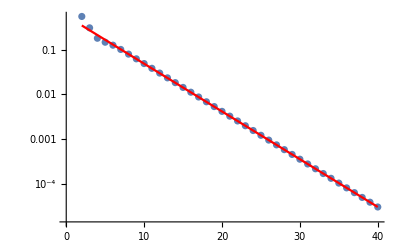

```mathematica
hPData=Table[{l,Sum[hPllLeft[l,m][rmin-r0] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],{m,-l,l}]},{l,2,lmax}];
paraFitRuleForPuncture = FindFit[Abs@hPData[[30;;All]],A Exp[-b l],{{A,0.003},{b,0.21}},l]
Show[
ListLogPlot[Abs@hPData],
LogPlot[{A Exp[-b l] /. paraFitRuleForPuncture},{l,2,lmax},PlotStyle->Red]
]
```

For the derivatives below, checked that substituting known values of derivatives of h^P, instead of differentiating the interpolating polynomials makes no difference.

{A→0.982314,b→0.21569}

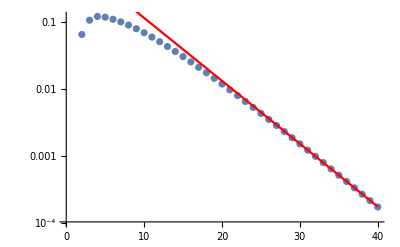

```mathematica
hPData=Table[{l,Sum[hPllLeft[l,m]'[rmin-r0] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],{m,-l,l}]},{l,2,lmax}];
paraFitRuleForPuncture = FindFit[Abs@hPData[[30;;All]],A Exp[-b l],{{A,0.003},{b,0.21}},l]
Show[
ListLogPlot[Abs@hPData],
LogPlot[{A Exp[-b l] /. paraFitRuleForPuncture},{l,2,lmax},PlotStyle->Red]
]
```

{A→1.64595,b→0.186073}

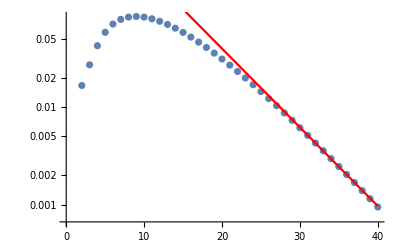

```mathematica
hPData=Table[{l,Sum[hPllLeft[l,m]''[rmin-r0] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],{m,-l,l}]},{l,2,lmax}];
paraFitRuleForPuncture = FindFit[Abs@hPData[[30;;All]],A Exp[-b l],{{A,0.003},{b,0.21}},l]
Show[
ListLogPlot[Abs@hPData],
LogPlot[{A Exp[-b l] /. paraFitRuleForPuncture},{l,2,lmax},PlotStyle->Red]
]
```

## Effective stress-energy

## Definitions

### Stress energy

Note: When defining the “TRXXInterpolation” below, important that the different geodesics and numerical quantities (r_0,M, etc) have not been set yet. Otherwise, get a strange error in T_ln which only uses 3 digits of precision.

```mathematica
Clear[TabRMatterVec,TabRδRminVec,TabRδpRminVec, TabRδRmaxVec,TabRδpRmaxVec,
TllWorldtubePiece,TlnWorldtubePiece,TlmWorldtubePiece,TlmbWorldtubePiece,TnnWorldtubePiece,TnmWorldtubePiece,TnmbWorldtubePiece,TmmWorldtubePiece,TmmbWorldtubePiece,TmbmbWorldtubePiece, (* Matter pieces *)
TllδRminPiece,TlnδRminPiece,TlmδRminPiece,TlmbδRminPiece,TnnδRminPiece,TnmδRminPiece,TnmbδRminPiece,TmmδRminPiece,TmmbδRminPiece,TmbmbδRminPiece,
TllδRmaxPiece,TlnδRmaxPiece,TlmδRmaxPiece,TlmbδRmaxPiece,TnnδRmaxPiece,TnmδRmaxPiece,TnmbδRmaxPiece,TmmδRmaxPiece,TmmbδRmaxPiece,TmbmbδRmaxPiece, (* δ pieces *)
TllδpRminPiece,TlnδpRminPiece,TlmδpRminPiece,TlmbδpRminPiece,TnnδpRminPiece,TnmδpRminPiece,TnmbδpRminPiece,TmmδpRminPiece,TmmbδpRminPiece,TmbmbδpRminPiece,
TllδpRmaxPiece,TlnδpRmaxPiece,TlmδpRmaxPiece,TlmbδpRmaxPiece,TnnδpRmaxPiece,TnmδpRmaxPiece,TnmbδpRmaxPiece,TmmδpRmaxPiece,TmmbδpRmaxPiece,TmbmbδpRmaxPiece] (* δ' pieces *)

TabRMatterVec = {TllWorldtubePiece,TlnWorldtubePiece,TlmWorldtubePiece,TlmbWorldtubePiece,TnnWorldtubePiece,TnmWorldtubePiece,TnmbWorldtubePiece,TmmWorldtubePiece,TmmbWorldtubePiece,TmbmbWorldtubePiece};
TabRδRminVec = {TllδRminPiece,TlnδRminPiece,TlmδRminPiece,TlmbδRminPiece,TnnδRminPiece,TnmδRminPiece,TnmbδRminPiece,TmmδRminPiece,TmmbδRminPiece,TmbmbδRminPiece};
TabRδpRminVec = {TllδpRminPiece,TlnδpRminPiece,TlmδpRminPiece,TlmbδpRminPiece,TnnδpRminPiece,TnmδpRminPiece,TnmbδpRminPiece,TmmδpRminPiece,TmmbδpRminPiece,TmbmbδpRminPiece};
TabRδRmaxVec = {TllδRmaxPiece,TlnδRmaxPiece,TlmδRmaxPiece,TlmbδRmaxPiece,TnnδRmaxPiece,TnmδRmaxPiece,TnmbδRmaxPiece,TmmδRmaxPiece,TmmbδRmaxPiece,TmbmbδRmaxPiece};
TabRδpRmaxVec = {TllδpRmaxPiece,TlnδpRmaxPiece,TlmδpRmaxPiece,TlmbδpRmaxPiece,TnnδpRmaxPiece,TnmδpRmaxPiece,TnmbδpRmaxPiece,TmmδpRmaxPiece,TmmbδpRmaxPiece,TmbmbδpRmaxPiece};
Do[Evaluate[TabRMatterVec[[iInd]]][l_,m_][r_] = -ℰhPWorldtubePiece[l,m][r][[iInd]],{iInd,1,Length[TabRMatterVec]}];
Do[Evaluate[TabRδRminVec[[iInd]]][l_,m_]   = -ℰhPδRminPiece[l,m][[iInd]],{iInd,1,Length[TabRδRminVec]}];
Do[Evaluate[TabRδpRminVec[[iInd]]][l_,m_] = -ℰhPδpRminPiece[l,m][[iInd]],{iInd,1,Length[TabRδpRminVec]}];
Do[Evaluate[TabRδRmaxVec[[iInd]]][l_,m_]   = -ℰhPδRmaxPiece[l,m][[iInd]],{iInd,1,Length[TabRδRmaxVec]}];
Do[Evaluate[TabRδpRmaxVec[[iInd]]][l_,m_] = -ℰhPδpRmaxPiece[l,m][[iInd]],{iInd,1,Length[TabRδpRmaxVec]}];
Clear[ℰhPWorldtubePiece,ℰhPδRminPiece,ℰhPδpRminPiece,ℰhPδRmaxPiece,ℰhPδpRmaxPiece]
```

### Large l behaviour of T_ll

Not evaluable.

Note: we ignore the large l behaviour of the metric perturbation and derivatives, effectively assuming they all have the same leading order behaviour.

```mathematica
Normal@Series[TllWorldtubePiece[l,m][r] ExpIωrstar[m][r]  /. g_[l,m] -> g,{l,∞,-2}] // Simplify
Normal@Series[TlmWorldtubePiece[l,m][r] ExpIωrstar[m][r] /. g_[l,m] -> g,{l,∞,-2}] // Simplify
Normal@Series[TlnWorldtubePiece[l,m][r] ExpIωrstar[m][r] /. g_[l,m] -> g,{l,∞,-2}] // Simplify
```

(l^2 h𝒫ll[r])/(2 r^2)

(l^2 (h𝒫lm[r]+h𝒫lmb[r]))/(4 r^2)

(l^2 (-2 h𝒫ln[r]+h𝒫mbmb[r]+h𝒫mm[r]+2 h𝒫mmb[r]))/(4 r^2)

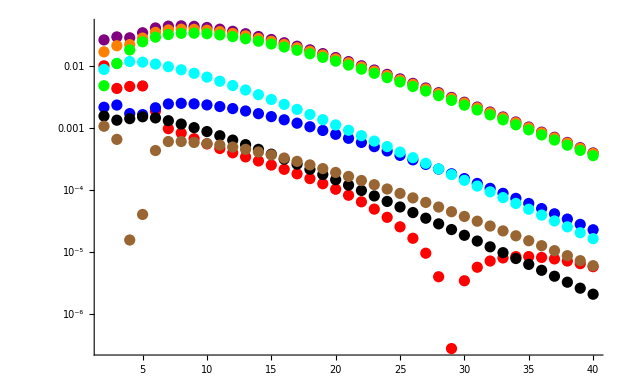

```mathematica
TllData=Table[{l,Sum[TllLeftInterpol[l,m][rmin] ExpIωrstar[m][rmin] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],{m,-l,l}]},{l,2,lmax}];
hPllData=Table[{l,Sum[ (l+l^2-2 ⅈ m rmin Ωφ)/(2 rmin^2)  hPllLeft[l,m][rmin-r0] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],{m,-l,l}]},{l,2,lmax}];
hPlnData=Table[{l,Sum[ -(2 ⅈ m Ωφ)/(2 M-rmin)  hPlnLeft[l,m][rmin-r0] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],{m,-l,l}]},{l,2,lmax}];
hPlmData=Table[{l,Sum[ (√(l (1+l)) (2 M+rmin (-1+ⅈ m rmin Ωφ)))/(√2 (2 M-rmin) rmin^2)  hPlmLeft[l,m][rmin-r0] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],{m,-l,l}]},{l,2,lmax}];
hPlnpData=Table[{l,Sum[-2/rmin  hPlnLeft[l,m]'[rmin-r0] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],{m,-l,l}]},{l,2,lmax}];
hPlmpData=Table[{l,Sum[(√(l (1+l)))/(√2 rmin)  hPlmLeft[l,m]'[rmin-r0] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],{m,-l,l}]},{l,2,lmax}];
hPmmbpData=Table[{l,Sum[-(4 M-2 rmin+2 ⅈ m rmin^2 Ωφ)/(2 M rmin-rmin^2)  hPmmbLeft[l,m]'[rmin-r0] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],{m,-l,l}]},{l,2,lmax}];
hPmmbppData=Table[{l,Sum[ -hPmmbLeft[l,m]''[rmin-r0] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],{m,-l,l}]},{l,2,lmax}];
hPLargelBehaviourData=Table[{l,Sum[ l^2/(2 rmin^2)  hPllLeft[l,m][rmin-r0] SpinWeightedSphericalHarmonicY[0,l,m,π/2,0],{m,-l,l}]},{l,2,lmax}];
Show[
ListLogPlot[Abs@TllData, PlotStyle -> Red],
ListLogPlot[Abs@hPllData,PlotStyle->Purple],
(*ListLogPlot[Abs@hPlnData,PlotStyle->Yellow],*)
ListLogPlot[Abs@hPlmData,PlotStyle->Blue],
ListLogPlot[Abs@hPlnpData,PlotStyle->Black],
ListLogPlot[Abs@hPlmpData,PlotStyle->Brown],
ListLogPlot[Abs@hPmmbpData,PlotStyle->Cyan],
ListLogPlot[Abs@hPLargelBehaviourData,PlotStyle->Orange],
ListLogPlot[Abs@hPmmbppData,PlotStyle->Green],
PlotRange -> All]
```

### Left and right interpolations

Hack: in the below, I use the assumption l≥2 when simplifying, even if this is not necessarily true for some quantities.
The reason is to force Mathematica to cancel out certain terms, which will otherwise give a 0/0 error (e.g. evaluating T_ln for l=0,1).

```mathematica
myruleLeft =
{h𝒫[x_][l_,m_][r_]-> hSLeftInterpol[x][l,m][r-r0],
h𝒫[x_][l_,m_]'[r_]-> dhSLeftInterpol[x][l,m][r-r0],
h𝒫[x_][l_,m_]''[r_]-> ddhSLeftInterpol[x][l,m][r-r0]};
myruleRight =
{h𝒫[x_][l_,m_][r_]-> hSRightInterpol[x][l,m][r-r0],
h𝒫[x_][l_,m_]'[r_]-> dhSRightInterpol[x][l,m][r-r0],
h𝒫[x_][l_,m_]''[r_]-> ddhSRightInterpol[x][l,m][r-r0]};
Clear[TllLeftInterpol,TlnLeftInterpol,TlmLeftInterpol,TlmbLeftInterpol,TnnLeftInterpol,TnmLeftInterpol,TnmbLeftInterpol,TmmLeftInterpol,TmmbLeftInterpol,TmbmbLeftInterpol,
TllRightInterpol,TlnRightInterpol,TlmRightInterpol,TlmbRightInterpol,TnnRightInterpol,TnmRightInterpol,TnmbRightInterpol,TmmRightInterpol,TmmbRightInterpol,TmbmbRightInterpol,
TllδRminInterpol,TlnδRminInterpol,TlmδRminInterpol,TlmbδRminInterpol,TnnδRminInterpol,TnmδRminInterpol,TnmbδRminInterpol,TmmδRminInterpol,TmmbδRminInterpol,TmbmbδRminInterpol,
TllδpRminInterpol,TlnδpRminInterpol,TlmδpRminInterpol,TlmbδpRminInterpol,TnnδpRminInterpol,TnmδpRminInterpol,TnmbδpRminInterpol,TmmδpRminInterpol,TmmbδpRminInterpol,TmbmbδpRminInterpol]
TllLeftInterpol[l_,m_][r_] = Simplify[TllWorldtubePiece[l,m][r]/. TetradToBLSRule,{l≥2}]  //.myruleLeft;
TlnLeftInterpol[l_,m_][r_] = Simplify[TlnWorldtubePiece[l,m][r]/. TetradToBLSRule,{l≥2}]  //.myruleLeft;
TlmLeftInterpol[l_,m_][r_] =Simplify[TlmWorldtubePiece[l,m][r]/. TetradToBLSRule,{l≥2}]  //.myruleLeft;
TlmbLeftInterpol[l_,m_][r_] = Simplify[TlmbWorldtubePiece[l,m][r]/. TetradToBLSRule,{l≥2}]  //.myruleLeft;
TnnLeftInterpol[l_,m_][r_] =Simplify[TnnWorldtubePiece[l,m][r]/. TetradToBLSRule,{l≥2}]  //.myruleLeft;
TnmLeftInterpol[l_,m_][r_] = Simplify[TnmWorldtubePiece[l,m][r]/. TetradToBLSRule,{l≥2}]  //.myruleLeft;
TnmbLeftInterpol[l_,m_][r_] =Simplify[TnmbWorldtubePiece[l,m][r]/. TetradToBLSRule,{l≥2}]  //.myruleLeft;
TmmLeftInterpol[l_,m_][r_] =Simplify[TmmWorldtubePiece[l,m][r]/. TetradToBLSRule,{l≥2}]  //.myruleLeft;
TmmbLeftInterpol[l_,m_][r_] = Simplify[TmmbWorldtubePiece[l,m][r]/. TetradToBLSRule,{l≥2}]  //.myruleLeft;
TmbmbLeftInterpol[l_,m_][r_] = Simplify[TmbmbWorldtubePiece[l,m][r]/. TetradToBLSRule,{l≥2}]  //.myruleLeft;

TllRightInterpol[l_,m_][r_] = Simplify[TllWorldtubePiece[l,m][r]/. TetradToBLSRule,{l≥2}]  //.myruleRight;
TlnRightInterpol[l_,m_][r_] = Simplify[TlnWorldtubePiece[l,m][r]/. TetradToBLSRule,{l≥2}]  //.myruleRight;
TlmRightInterpol[l_,m_][r_] = Simplify[TlmWorldtubePiece[l,m][r]/. TetradToBLSRule,{l≥2}]  //.myruleRight;
TlmbRightInterpol[l_,m_][r_] = Simplify[TlmbWorldtubePiece[l,m][r]/. TetradToBLSRule,{l≥2}]  //.myruleRight;
TnnRightInterpol[l_,m_][r_] = Simplify[TnnWorldtubePiece[l,m][r]/. TetradToBLSRule,{l≥2}]  //.myruleRight;
TnmRightInterpol[l_,m_][r_] = Simplify[TnmWorldtubePiece[l,m][r]/. TetradToBLSRule,{l≥2}]  //.myruleRight;
TnmbRightInterpol[l_,m_][r_] = Simplify[TnmbWorldtubePiece[l,m][r]/. TetradToBLSRule,{l≥2}]  //.myruleRight;
TmmRightInterpol[l_,m_][r_] = Simplify[TmmWorldtubePiece[l,m][r]/. TetradToBLSRule,{l≥2}]  //.myruleRight;
TmmbRightInterpol[l_,m_][r_] = Simplify[TmmbWorldtubePiece[l,m][r]/. TetradToBLSRule,{l≥2}]  //.myruleRight;
TmbmbRightInterpol[l_,m_][r_] =Simplify[TmbmbWorldtubePiece[l,m][r]/. TetradToBLSRule,{l≥2}]  //.myruleRight;

TllδRminInterpol[l_,m_] =Simplify[TllδRminPiece[l,m]/. TetradToBLSRule,{l≥2}]  //.myruleLeft;
TlnδRminInterpol[l_,m_] = Simplify[TlnδRminPiece[l,m]/. TetradToBLSRule,{l≥2}]  //.myruleLeft;
TlmδRminInterpol[l_,m_] = Simplify[TlmδRminPiece[l,m]/. TetradToBLSRule,{l≥2}]  //.myruleLeft;
TlmbδRminInterpol[l_,m_] = Simplify[TlmbδRminPiece[l,m]/. TetradToBLSRule,{l≥2}]  //.myruleLeft;
TnnδRminInterpol[l_,m_] = Simplify[TnnδRminPiece[l,m]/. TetradToBLSRule,{l≥2}]  //.myruleLeft;
TnmδRminInterpol[l_,m_] = Simplify[TnmδRminPiece[l,m]/. TetradToBLSRule,{l≥2}]  //.myruleLeft;
TnmbδRminInterpol[l_,m_] = Simplify[TnmbδRminPiece[l,m]/. TetradToBLSRule,{l≥2}]  //.myruleLeft;
TmmδRminInterpol[l_,m_] = Simplify[TmmδRminPiece[l,m]/. TetradToBLSRule,{l≥2}]  //.myruleLeft;
TmmbδRminInterpol[l_,m_] = Simplify[TmmbδRminPiece[l,m]/. TetradToBLSRule,{l≥2}]  //.myruleLeft;
TmbmbδRminInterpol[l_,m_] = Simplify[TmbmbδRminPiece[l,m]/. TetradToBLSRule,{l≥2}]  //.myruleLeft;

TllδpRminInterpol[l_,m_] = Simplify[TllδpRminPiece[l,m]/. TetradToBLSRule,{l≥2}]  //.myruleLeft;
TlnδpRminInterpol[l_,m_] = Simplify[TlnδpRminPiece[l,m]/. TetradToBLSRule,{l≥2}]  //.myruleLeft;
TlmδpRminInterpol[l_,m_] = Simplify[TlmδpRminPiece[l,m]/. TetradToBLSRule,{l≥2}]  //.myruleLeft;
TlmbδpRminInterpol[l_,m_] = Simplify[TlmbδpRminPiece[l,m]/. TetradToBLSRule,{l≥2}]  //.myruleLeft;
TnnδpRminInterpol[l_,m_] = Simplify[TnnδpRminPiece[l,m]/. TetradToBLSRule,{l≥2}]  //.myruleLeft;
TnmδpRminInterpol[l_,m_] = Simplify[TnmδpRminPiece[l,m]/. TetradToBLSRule,{l≥2}]  //.myruleLeft;
TnmbδpRminInterpsol[l_,m_] = Simplify[TnmbδpRminPiece[l,m]/. TetradToBLSRule,{l≥2}]  //.myruleLeft;
TmmδpRminInterpol[l_,m_] = Simplify[TmmδpRminPiece[l,m]/. TetradToBLSRule,{l≥2}]  //.myruleLeft;
TmmbδpRminInterpol[l_,m_] = Simplify[TmmbδpRminPiece[l,m]/. TetradToBLSRule,{l≥2}]  //.myruleLeft;
TmbmbδpRminInterpol[l_,m_] = Simplify[TmbmbδpRminPiece[l,m]/. TetradToBLSRule,{l≥2}]  //.myruleLeft;

Clear[TllδRmaxInterpol,TllδpRmaxInterpol,TlmδRmaxInterpol,TlmδpRmaxInterpol,TlnδRmaxInterpol,TlnδpRmaxInterpol,TnnδRmaxInterpol,TnnδpRmaxInterpol,TnmδRmaxInterpol,TnmδpRmaxInterpol,TnmbδRmaxInterpol,TnmbδpRmaxInterpol]
TllδRmaxInterpol[l_,m_] =Simplify[TllδRmaxPiece[l,m]/. TetradToBLSRule,{l≥2}]  //.myruleRight;
TlmδRmaxInterpol[l_,m_] =Simplify[TlmδRmaxPiece[l,m]/. TetradToBLSRule,{l≥2}]  //.myruleRight;
TlmbδRmaxInterpol[l_,m_] =Simplify[TlmbδRmaxPiece[l,m]/. TetradToBLSRule,{l≥2}]  //.myruleRight;
TlnδRmaxInterpol[l_,m_] =Simplify[TlnδRmaxPiece[l,m]/. TetradToBLSRule,{l≥2}]  //.myruleRight;
TnnδRmaxInterpol[l_,m_] =Simplify[TnnδRmaxPiece[l,m]/. TetradToBLSRule,{l≥2}]  //.myruleRight;
TnmδRmaxInterpol[l_,m_] =Simplify[TnmδRmaxPiece[l,m]/. TetradToBLSRule,{l≥2}]  //.myruleRight;
TnmbδRmaxInterpol[l_,m_] =Simplify[TnmbδRmaxPiece[l,m]/. TetradToBLSRule,{l≥2}]  //.myruleRight;

TllδpRmaxInterpol[l_,m_] =Simplify[TllδpRmaxPiece[l,m]/. TetradToBLSRule,{l≥2}]  //.myruleRight;
TlmδpRmaxInterpol[l_,m_] =Simplify[TlmδpRmaxPiece[l,m]/. TetradToBLSRule,{l≥2}]  //.myruleRight;
TlmbδpRmaxInterpol[l_,m_] =Simplify[TlmbδpRmaxPiece[l,m]/. TetradToBLSRule,{l≥2}]  //.myruleRight;
TlnδpRmaxInterpol[l_,m_] =Simplify[TlnδpRmaxPiece[l,m]/. TetradToBLSRule,{l≥2}]  //.myruleRight;
TnnδpRmaxInterpol[l_,m_] =Simplify[TnnδpRmaxPiece[l,m]/. TetradToBLSRule,{l≥2}]  //.myruleRight;
TnmδpRmaxInterpol[l_,m_] =Simplify[TnmδpRmaxPiece[l,m]/. TetradToBLSRule,{l≥2}]  //.myruleRight;
TnmbδpRmaxInterpol[l_,m_] =Simplify[TnmbδpRmaxPiece[l,m]/. TetradToBLSRule,{l≥2}]  //.myruleRight;
```

## m-mode effective source numerics

```mathematica
Clear[ExpIωrstar,rstar]
rstar[r_] = r+2M Log[r/(2M)-1]
ExpIωrstar[m_][r_] = Exp[I ωm[m] rstar[r]];
```

r+2 M Log[-1+r/(2 M)]

## mode-sums

```mathematica
Lmax=30;
```

```mathematica
r0=10
```

10

```mathematica
Clear[sumOverLNow]

sumOverLNow[expr_,m_,{l_,lmin_,lmax_}]:=If[Abs[m]>lmax,0,Sum[expr,{l,Max[lmin,Abs[m]],lmax}]];
```

```mathematica
Clear[rBufferGrid, Nbuff]
```

```mathematica
Clear[Teff$WorldTube$ll,Teff$WorldTube$ln,Teff$WorldTube$lm,Teff$WorldTube$lm,Teff$WorldTube$lmb,Teff$WorldTube$nn,Teff$WorldTube$nm, Teff$WorldTube$nmb,Teff$WorldTube$mm, Teff$WorldTube$mmb, Teff$WorldTube$mbmb, Teff$WorldTubeVec, Teff$δpRmin$ll, Teff$δpRmin$ln, Teff$δpRmin$lm, Teff$δpRmin$lmb, Teff$δpRmin$nn, Teff$δpRmin$nm, Teff$δpRmin$nmb, Teff$δpRmin$mm, Teff$δpRmin$mmb, Teff$δpRmin$mbmb,Teff$δRmin$ll, Teff$δRmin$ln, Teff$δRmin$lm, Teff$δRmin$lmb, Teff$δRmin$nn, Teff$δRmin$nm, Teff$δRmin$nmb, Teff$δRmin$mm, Teff$δRmin$mmb, Teff$δRmin$mbmb,  Teff$δpRmax$ll, Teff$δpRmax$ln, Teff$δpRmax$lm, Teff$δpRmax$lmb, Teff$δpRmax$nn, Teff$δpRmax$nm, Teff$δpRmax$nmb, Teff$δpRmax$mm, Teff$δpRmax$mmb, Teff$δRmax$mbmb,Teff$δRmax$ll, Teff$δRmax$ln, Teff$δRmax$lm, Teff$δRmax$lmb, Teff$δRmax$nn, Teff$δRmax$nm, Teff$pRmax$nmb, Teff$δRmax$mm, Teff$δRmax$mmb, Teff$δRmax$mbmb ]

Teff$WorldTube$ll[l_,m_][r_] = Piecewise[{{TllLeftInterpol[l,m][r],rmin<r<=r0},{TllRightInterpol[l,m][r],r0<r<rmax}}];
Teff$WorldTube$ln[l_,m_][r_] = Piecewise[{{TlnLeftInterpol[l,m][r],rmin<r<=r0},{TlnRightInterpol[l,m][r],r0<r<rmax}}];
Teff$WorldTube$lm[l_,m_][r_] = Piecewise[{{TlmLeftInterpol[l,m][r],rmin<r<=r0},{TlmRightInterpol[l,m][r],r0<r<rmax}}];
Teff$WorldTube$lmb[l_,m_][r_] = Piecewise[{{TlmbLeftInterpol[l,m][r],rmin<r<=r0},{TlmbRightInterpol[l,m][r],r0<r<rmax}}];
Teff$WorldTube$nn[l_,m_][r_] = Piecewise[{{TnnLeftInterpol[l,m][r],rmin<r<=r0},{TnnRightInterpol[l,m][r],r0<r<rmax}}];
Teff$WorldTube$nm[l_,m_][r_] = Piecewise[{{TnmLeftInterpol[l,m][r],rmin<r<=r0},{TnmRightInterpol[l,m][r],r0<r<rmax}}];
Teff$WorldTube$nmb[l_,m_][r_] = Piecewise[{{TnmbLeftInterpol[l,m][r],rmin<r<=r0},{TnmbRightInterpol[l,m][r],r0<r<rmax}}];
Teff$WorldTube$mm[l_,m_][r_] = Piecewise[{{TmmLeftInterpol[l,m][r],rmin<r<=r0},{TmmRightInterpol[l,m][r],r0<r<rmax}}];
Teff$WorldTube$mmb[l_,m_][r_] = Piecewise[{{TmmbLeftInterpol[l,m][r],rmin<r<=r0},{TmmbRightInterpol[l,m][r],r0<r<rmax}}];
Teff$WorldTube$mbmb[l_,m_][r_] = Piecewise[{{TmbmbLeftInterpol[l,m][r],rmin<r<=r0},{TmbmbRightInterpol[l,m][r],r0<r<rmax}}];

Teff$δRmin$ll[l_,m_]:=TllδRminInterpol[l,m]
Teff$δRmin$ln[l_,m_]:=TlnδRminInterpol[l,m]
Teff$δRmin$lm[l_,m_]:=TlmδRminInterpol[l,m]
Teff$δRmin$lmb[l_,m_]:=TlmbδRminInterpol[l,m]

Teff$δpRmin$ll[l_,m_]:=TllδpRminInterpol[l,m]
Teff$δpRmin$ln[l_,m_]:=TlnδpRminInterpol[l,m]
Teff$δpRmin$lm[l_,m_]:=TlmδpRminInterpol[l,m]
Teff$δpRmin$lmb[l_,m_]:=TlmbδpRminInterpol[l,m]

Teff$WorldTubeVec[l_,m_][r_] = {
	Teff$WorldTube$ll[l,m][r], 
	Teff$WorldTube$ln[l,m][r],
	Teff$WorldTube$lm[l,m][r],
	Teff$WorldTube$lmb[l,m][r],
	Teff$WorldTube$nn[l,m][r],
	Teff$WorldTube$nm[l,m][r],
	Teff$WorldTube$nmb[l,m][r],
	Teff$WorldTube$mm[l,m][r],
	Teff$WorldTube$mmb[l,m][r],
	Teff$WorldTube$mbmb[l,m][r]};
```

```mathematica
Clear[Teff$WorldTube$ll$mMode, Teff$WorldTube$ln$mMode,Teff$WorldTube$lm$mMode,Teff$WorldTube$lmb$mMode,  Teff$δpRmin$ll$mMode, Teff$δpRmin$ln$mMode,Teff$δpRmin$lm$mMode, Teff$δpRmin$lmb$mMode, Teff$δRmin$ll$mMode, Teff$δRmin$ln$mMode,Teff$δRmin$lm$mMode,Teff$δRmin$lmb$mMode]


Teff$WorldTube$ll$mMode[m_][r_]:=sumOverLNow[Teff$WorldTube$ll[l,m][r],m,{l,0,lmax}]
Teff$WorldTube$ln$mMode[m_][r_]:=sumOverLNow[Teff$WorldTube$ll[l,m][r],m,{l,0,lmax}]
Teff$WorldTube$lm$mMode[m_][r_]:=sumOverLNow[Teff$WorldTube$ll[l,m][r],m,{l,1,lmax}]
Teff$WorldTube$lmb$mMode[m_][r_]:=sumOverLNow[Teff$WorldTube$ll[l,m][r],m,{l,1,lmax}]


Teff$δRmin$ll$mMode[m_]:=sumOverLNow[Teff$δRmin$ll[l,m],m,{l,0,lmax}]
Teff$δRmin$ln$mMode[m_]:=sumOverLNow[Teff$δRmin$ln[l,m],m,{l,0,lmax}]
Teff$δRmin$lm$mMode[m_]:=sumOverLNow[Teff$δRmin$lm[l,m],m,{l,1,lmax}]
Teff$δRmin$lmb$mMode[m_]:=sumOverLNow[Teff$δRmin$lmb[l,m],m,{l,1,lmax}]

Teff$δpRmin$ll$mMode[m_]:=sumOverLNow[Teff$δpRmin$ll[l,m],m,{l,0,lmax}]
Teff$δpRmin$ln$mMode[m_]:=sumOverLNow[Teff$δpRmin$ln[l,m],m,{l,0,lmax}]
Teff$δpRmin$lm$mMode[m_]:=sumOverLNow[Teff$δpRmin$lm[l,m],m,{l,1,lmax}]
Teff$δpRmin$lmb$mMode[m_]:=sumOverLNow[Teff$δpRmin$lmb[l,m],m,{l,1,lmax}]
```

## Set numerical quantities

```mathematica
<<KerrGeodesics`
```

Computation of the appropriate frequencies, energies and geodesics.

```mathematica
Clear[lmax,aKerr,wp,M,r0,rmin,rmax,p0,e0,rNumOutbd,rNumInbd,ρmin,ρmax,ρ0,eccentricity,ar,aϕ,at,Ωr,Ωθ,Ωφ,Orbit]
```

```mathematica
lmax=40;
lmaxCorrectorTensors=lmax;
```

```mathematica
aKerr=0;
wp = 64;
```

```mathematica
M=1;
r0=10 M; (* Make sure this is consistent with myr0 from puncture *)
rmin = r0-2M;
rmax = r0+2 M;
p0 = N[r0,wp]; (* approx needed if r0 and M are exact. *)
e0=0;
Ωφ2Rule = Ωφ^2 -> M/r0^3;
Δr[r_]=r-r0;
ωm[m_]= m Ωφ;
rNumInbd = rmin-2 M; (* numerical inner boundary *)
rNumOutbd = rmax+2 M; 

(* numerical outer boundary *)
```

```mathematica
ρmin = ρOfrK[rmin];
ρmax = ρOfrK[rmax];
ρ0 = ρOfrK[r0];
eccentricity=0;
```

```mathematica
ar=aϕ=at=0;
```

```mathematica
{Ωr,Ωθ,Ωφ}=Values[KerrGeoFrequencies[0,p0,eccentricity,1]];
```

```mathematica
Orbit=KerrGeoOrbit[aKerr,p0,eccentricity,1];
```

```mathematica
Teff$WorldTube$lmb$mMode[10][11]
```

-0.0000201989+0.0000323533 ⅈ